```mathematica
ClearAll["Global`*"]
P=Subscript[c, 1]/(Subscript[x, 1]-Subscript[A, 1]) + Subscript[c, 2]/(Subscript[x, 2]-Subscript[A, 2]) (Subscript[x, 1]+Subscript[B, 1])/(Subscript[x, 1]-Subscript[A, 1]) + Subscript[c, 3]/(Subscript[x, 3]-Subscript[A, 3])(Subscript[x, 1]+Subscript[B, 1])/(Subscript[x, 1]-Subscript[A, 1])(Subscript[x, 2]+Subscript[B, 2])/(Subscript[x, 2]-Subscript[A, 2])
Q=P/.{Subscript[x, 1]->λ Subscript[y, 1],Subscript[x, 2]->λ Subscript[x, 2],Subscript[x, 3]->λ Subscript[x, 3]}
S =Subscript[x, 1]+Subscript[x, 2] +Subscript[x, 3]- λ (Subscript[y, 1]+Subscript[x, 2]+Subscript[x, 3])

diff23=FactorList[Numerator[D[P,Subscript[x, 2]]-D[P,Subscript[x, 3]]//Factor]];
diff23=diff23[[3]][[1]]
c3sol=Solve[diff23==0,Subscript[c, 3]][[1]]
PQ=Numerator[Factor[(P-Q)/.c3sol]]

diff=D[P,Subscript[x, 1]]-D[P,Subscript[x, 3]];
diff=FactorList[Numerator[Factor[diff/.{Subscript[x, 1]->Subscript[y, 1]}/.c3sol]]];
diff=diff[[2]][[1]]

y1sol=Solve[S==0,Subscript[y, 1]]

opteqlambda=Numerator[Factor[diff/.y1sol]]
```

c_1/(-A_1+x_1)+(c_2 (B_1+x_1))/((-A_1+x_1) (-A_2+x_2))+(c_3 (B_1+x_1) (B_2+x_2))/((-A_1+x_1) (-A_2+x_2) (-A_3+x_3))

c_1/(-A_1+λ y_1)+(c_2 (B_1+λ y_1))/((-A_2+λ x_2) (-A_1+λ y_1))+(c_3 (B_2+λ x_2) (B_1+λ y_1))/((-A_2+λ x_2) (-A_3+λ x_3) (-A_1+λ y_1))

x_1+x_2+x_3-λ (x_2+x_3+y_1)

A_3^2 c_2-A_2 A_3 c_3+A_2 B_2 c_3-A_3 B_2 c_3+A_2 c_3 x_2-B_2 c_3 x_2-c_3 x_2^2-2 A_3 c_2 x_3+A_2 c_3 x_3+B_2 c_3 x_3+c_2 x_3^2

{c_3→(A_3^2 c_2-2 A_3 c_2 x_3+c_2 x_3^2)/(A_2 A_3-A_2 B_2+A_3 B_2-A_2 x_2+B_2 x_2+x_2^2-A_2 x_3-B_2 x_3)}

A_2^2 A_3^2 c_1 x_1-A_2^2 A_3 B_2 c_1 x_1+A_2 A_3^2 B_2 c_1 x_1-A_1 A_2 A_3^2 c_2 x_1-A_2 A_3^2 B_1 c_2 x_1+A_1 A_2 A_3 B_2 c_2 x_1+A_2 A_3 B_1 B_2 c_2 x_1+A_1 A_3 B_1 B_2 c_2 x_2-λ A_1 A_3 B_1 B_2 c_2 x_2-A_2^2 A_3 c_1 x_1 x_2-λ A_2 A_3^2 c_1 x_1 x_2+A_2 A_3 B_2 c_1 x_1 x_2+λ A_2 A_3 B_2 c_1 x_1 x_2-λ A_3^2 B_2 c_1 x_1 x_2+A_1 A_2 A_3 c_2 x_1 x_2+λ A_1 A_3^2 c_2 x_1 x_2+A_2 A_3 B_1 c_2 x_1 x_2+λ A_3^2 B_1 c_2 x_1 x_2-λ A_1 A_3 B_2 c_2 x_1 x_2-A_3 B_1 B_2 c_2 x_1 x_2+A_1 A_3 B_1 c_2 x_2^2-λ A_1 A_3 B_1 c_2 x_2^2+A_2 A_3 c_1 x_1 x_2^2+λ A_2 A_3 c_1 x_1 x_2^2-λ A_3 B_2 c_1 x_1 x_2^2-λ A_1 A_3 c_2 x_1 x_2^2-A_3 B_1 c_2 x_1 x_2^2-λ A_3 c_1 x_1 x_2^3+A_1 A_3 B_1 B_2 c_2 x_3-λ A_1 A_3 B_1 B_2 c_2 x_3-A_2^2 A_3 c_1 x_1 x_3-λ A_2^2 A_3 c_1 x_1 x_3+λ A_2^2 B_2 c_1 x_1 x_3-A_2 A_3 B_2 c_1 x_1 x_3-λ A_2 A_3 B_2 c_1 x_1 x_3+A_1 A_2 A_3 c_2 x_1 x_3+λ A_1 A_2 A_3 c_2 x_1 x_3+A_2 A_3 B_1 c_2 x_1 x_3+λ A_2 A_3 B_1 c_2 x_1 x_3-λ A_1 A_2 B_2 c_2 x_1 x_3-λ A_2 B_1 B_2 c_2 x_1 x_3-A_3 B_1 B_2 c_2 x_1 x_3+λ A_3 B_1 B_2 c_2 x_1 x_3+λ A_1 A_3 B_1 c_2 x_2 x_3-λ^2 A_1 A_3 B_1 c_2 x_2 x_3-λ A_1 B_1 B_2 c_2 x_2 x_3+λ^2 A_1 B_1 B_2 c_2 x_2 x_3+λ A_2^2 c_1 x_1 x_2 x_3+λ A_2 A_3 c_1 x_1 x_2 x_3+λ^2 A_2 A_3 c_1 x_1 x_2 x_3-λ A_2 B_2 c_1 x_1 x_2 x_3-λ^2 A_2 B_2 c_1 x_1 x_2 x_3+λ A_3 B_2 c_1 x_1 x_2 x_3+λ^2 A_3 B_2 c_1 x_1 x_2 x_3-λ A_1 A_2 c_2 x_1 x_2 x_3-λ A_1 A_3 c_2 x_1 x_2 x_3-λ^2 A_1 A_3 c_2 x_1 x_2 x_3-λ A_2 B_1 c_2 x_1 x_2 x_3-2 λ A_3 B_1 c_2 x_1 x_2 x_3+λ^2 A_1 B_2 c_2 x_1 x_2 x_3+λ B_1 B_2 c_2 x_1 x_2 x_3-λ A_1 B_1 c_2 x_2^2 x_3+λ^2 A_1 B_1 c_2 x_2^2 x_3-λ A_2 c_1 x_1 x_2^2 x_3-λ^2 A_2 c_1 x_1 x_2^2 x_3+λ^2 B_2 c_1 x_1 x_2^2 x_3+λ^2 A_1 c_2 x_1 x_2^2 x_3+λ B_1 c_2 x_1 x_2^2 x_3+λ^2 c_1 x_1 x_2^3 x_3-A_1 B_1 B_2 c_2 x_3^2+λ A_1 B_1 B_2 c_2 x_3^2+λ A_2^2 c_1 x_1 x_3^2+λ A_2 B_2 c_1 x_1 x_3^2-λ A_1 A_2 c_2 x_1 x_3^2-λ A_2 B_1 c_2 x_1 x_3^2+B_1 B_2 c_2 x_1 x_3^2-λ B_1 B_2 c_2 x_1 x_3^2-λ A_1 B_1 c_2 x_2 x_3^2+λ^2 A_1 B_1 c_2 x_2 x_3^2-λ^2 A_2 c_1 x_1 x_2 x_3^2-λ^2 B_2 c_1 x_1 x_2 x_3^2+λ^2 A_1 c_2 x_1 x_2 x_3^2+λ B_1 c_2 x_1 x_2 x_3^2-λ A_2^2 A_3^2 c_1 y_1+λ A_2^2 A_3 B_2 c_1 y_1-λ A_2 A_3^2 B_2 c_1 y_1+λ A_1 A_2 A_3^2 c_2 y_1+λ A_2 A_3^2 B_1 c_2 y_1-λ A_1 A_2 A_3 B_2 c_2 y_1-λ A_2 A_3 B_1 B_2 c_2 y_1+λ A_2^2 A_3 c_1 x_2 y_1+λ^2 A_2 A_3^2 c_1 x_2 y_1-λ A_2 A_3 B_2 c_1 x_2 y_1-λ^2 A_2 A_3 B_2 c_1 x_2 y_1+λ^2 A_3^2 B_2 c_1 x_2 y_1-λ A_1 A_2 A_3 c_2 x_2 y_1-λ^2 A_1 A_3^2 c_2 x_2 y_1-λ A_2 A_3 B_1 c_2 x_2 y_1-λ^2 A_3^2 B_1 c_2 x_2 y_1+λ A_1 A_3 B_2 c_2 x_2 y_1+λ^2 A_3 B_1 B_2 c_2 x_2 y_1-λ A_3 B_2 c_2 x_1 x_2 y_1+λ^2 A_3 B_2 c_2 x_1 x_2 y_1-λ A_2 A_3 c_1 x_2^2 y_1-λ^2 A_2 A_3 c_1 x_2^2 y_1+λ^2 A_3 B_2 c_1 x_2^2 y_1+λ A_1 A_3 c_2 x_2^2 y_1+λ^2 A_3 B_1 c_2 x_2^2 y_1-λ A_3 c_2 x_1 x_2^2 y_1+λ^2 A_3 c_2 x_1 x_2^2 y_1+λ^2 A_3 c_1 x_2^3 y_1+λ A_2^2 A_3 c_1 x_3 y_1+λ^2 A_2^2 A_3 c_1 x_3 y_1-λ^2 A_2^2 B_2 c_1 x_3 y_1+λ A_2 A_3 B_2 c_1 x_3 y_1+λ^2 A_2 A_3 B_2 c_1 x_3 y_1-λ A_1 A_2 A_3 c_2 x_3 y_1-λ^2 A_1 A_2 A_3 c_2 x_3 y_1-λ A_2 A_3 B_1 c_2 x_3 y_1-λ^2 A_2 A_3 B_1 c_2 x_3 y_1+λ^2 A_1 A_2 B_2 c_2 x_3 y_1+λ A_1 A_3 B_2 c_2 x_3 y_1-λ^2 A_1 A_3 B_2 c_2 x_3 y_1+λ^2 A_2 B_1 B_2 c_2 x_3 y_1-λ A_3 B_2 c_2 x_1 x_3 y_1+λ^2 A_3 B_2 c_2 x_1 x_3 y_1-λ^2 A_2^2 c_1 x_2 x_3 y_1-λ^2 A_2 A_3 c_1 x_2 x_3 y_1-λ^3 A_2 A_3 c_1 x_2 x_3 y_1+λ^2 A_2 B_2 c_1 x_2 x_3 y_1+λ^3 A_2 B_2 c_1 x_2 x_3 y_1-λ^2 A_3 B_2 c_1 x_2 x_3 y_1-λ^3 A_3 B_2 c_1 x_2 x_3 y_1+λ^2 A_1 A_2 c_2 x_2 x_3 y_1+2 λ^2 A_1 A_3 c_2 x_2 x_3 y_1+λ^2 A_2 B_1 c_2 x_2 x_3 y_1+λ^2 A_3 B_1 c_2 x_2 x_3 y_1+λ^3 A_3 B_1 c_2 x_2 x_3 y_1-λ^2 A_1 B_2 c_2 x_2 x_3 y_1-λ^3 B_1 B_2 c_2 x_2 x_3 y_1-λ^2 A_3 c_2 x_1 x_2 x_3 y_1+λ^3 A_3 c_2 x_1 x_2 x_3 y_1+λ^2 B_2 c_2 x_1 x_2 x_3 y_1-λ^3 B_2 c_2 x_1 x_2 x_3 y_1+λ^2 A_2 c_1 x_2^2 x_3 y_1+λ^3 A_2 c_1 x_2^2 x_3 y_1-λ^3 B_2 c_1 x_2^2 x_3 y_1-λ^2 A_1 c_2 x_2^2 x_3 y_1-λ^3 B_1 c_2 x_2^2 x_3 y_1+λ^2 c_2 x_1 x_2^2 x_3 y_1-λ^3 c_2 x_1 x_2^2 x_3 y_1-λ^3 c_1 x_2^3 x_3 y_1-λ^2 A_2^2 c_1 x_3^2 y_1-λ^2 A_2 B_2 c_1 x_3^2 y_1+λ^2 A_1 A_2 c_2 x_3^2 y_1+λ^2 A_2 B_1 c_2 x_3^2 y_1-λ A_1 B_2 c_2 x_3^2 y_1+λ^2 A_1 B_2 c_2 x_3^2 y_1+λ B_2 c_2 x_1 x_3^2 y_1-λ^2 B_2 c_2 x_1 x_3^2 y_1+λ^3 A_2 c_1 x_2 x_3^2 y_1+λ^3 B_2 c_1 x_2 x_3^2 y_1-λ^2 A_1 c_2 x_2 x_3^2 y_1-λ^3 B_1 c_2 x_2 x_3^2 y_1+λ^2 c_2 x_1 x_2 x_3^2 y_1-λ^3 c_2 x_1 x_2 x_3^2 y_1

A_2^2 A_3 c_1-A_2^2 B_2 c_1+A_2 A_3 B_2 c_1-A_1 A_2 A_3 c_2-A_2 A_3 B_1 c_2+A_1 A_2 B_2 c_2-A_1 B_1 B_2 c_2+A_2 B_1 B_2 c_2-A_2^2 c_1 x_2-A_2 A_3 c_1 x_2+2 A_2 B_2 c_1 x_2-A_3 B_2 c_1 x_2+A_1 A_2 c_2 x_2+A_1 A_3 c_2 x_2-A_1 B_1 c_2 x_2+A_2 B_1 c_2 x_2+A_3 B_1 c_2 x_2-A_1 B_2 c_2 x_2-B_1 B_2 c_2 x_2+2 A_2 c_1 x_2^2-B_2 c_1 x_2^2-A_1 c_2 x_2^2-B_1 c_2 x_2^2-c_1 x_2^3-A_2^2 c_1 x_3-A_2 B_2 c_1 x_3+A_1 A_2 c_2 x_3+A_2 B_1 c_2 x_3+A_2 c_1 x_2 x_3+B_2 c_1 x_2 x_3-A_1 c_2 x_2 x_3-B_1 c_2 x_2 x_3-A_1 B_2 c_2 y_1+B_1 B_2 c_2 y_1-A_1 c_2 x_2 y_1+B_1 c_2 x_2 y_1+B_2 c_2 y_1^2+c_2 x_2 y_1^2

{{y_1→(x_1+x_2-λ x_2+x_3-λ x_3)/λ}}

{λ^2 A_2^2 A_3 c_1-λ^2 A_2^2 B_2 c_1+λ^2 A_2 A_3 B_2 c_1-λ^2 A_1 A_2 A_3 c_2-λ^2 A_2 A_3 B_1 c_2+λ^2 A_1 A_2 B_2 c_2-λ^2 A_1 B_1 B_2 c_2+λ^2 A_2 B_1 B_2 c_2-λ A_1 B_2 c_2 x_1+λ B_1 B_2 c_2 x_1+B_2 c_2 x_1^2-λ^2 A_2^2 c_1 x_2-λ^2 A_2 A_3 c_1 x_2+2 λ^2 A_2 B_2 c_1 x_2-λ^2 A_3 B_2 c_1 x_2+λ^2 A_1 A_2 c_2 x_2+λ^2 A_1 A_3 c_2 x_2-λ^2 A_1 B_1 c_2 x_2+λ^2 A_2 B_1 c_2 x_2+λ^2 A_3 B_1 c_2 x_2-λ A_1 B_2 c_2 x_2+λ B_1 B_2 c_2 x_2-2 λ^2 B_1 B_2 c_2 x_2-λ A_1 c_2 x_1 x_2+λ B_1 c_2 x_1 x_2+2 B_2 c_2 x_1 x_2-2 λ B_2 c_2 x_1 x_2+c_2 x_1^2 x_2+2 λ^2 A_2 c_1 x_2^2-λ^2 B_2 c_1 x_2^2-λ A_1 c_2 x_2^2+λ B_1 c_2 x_2^2-2 λ^2 B_1 c_2 x_2^2+B_2 c_2 x_2^2-2 λ B_2 c_2 x_2^2+λ^2 B_2 c_2 x_2^2+2 c_2 x_1 x_2^2-2 λ c_2 x_1 x_2^2-λ^2 c_1 x_2^3+c_2 x_2^3-2 λ c_2 x_2^3+λ^2 c_2 x_2^3-λ^2 A_2^2 c_1 x_3-λ^2 A_2 B_2 c_1 x_3+λ^2 A_1 A_2 c_2 x_3+λ^2 A_2 B_1 c_2 x_3-λ A_1 B_2 c_2 x_3+λ^2 A_1 B_2 c_2 x_3+λ B_1 B_2 c_2 x_3-λ^2 B_1 B_2 c_2 x_3+2 B_2 c_2 x_1 x_3-2 λ B_2 c_2 x_1 x_3+λ^2 A_2 c_1 x_2 x_3+λ^2 B_2 c_1 x_2 x_3-λ A_1 c_2 x_2 x_3+λ B_1 c_2 x_2 x_3-2 λ^2 B_1 c_2 x_2 x_3+2 B_2 c_2 x_2 x_3-4 λ B_2 c_2 x_2 x_3+2 λ^2 B_2 c_2 x_2 x_3+2 c_2 x_1 x_2 x_3-2 λ c_2 x_1 x_2 x_3+2 c_2 x_2^2 x_3-4 λ c_2 x_2^2 x_3+2 λ^2 c_2 x_2^2 x_3+B_2 c_2 x_3^2-2 λ B_2 c_2 x_3^2+λ^2 B_2 c_2 x_3^2+c_2 x_2 x_3^2-2 λ c_2 x_2 x_3^2+λ^2 c_2 x_2 x_3^2}

```mathematica
xxi={Subscript[x, 1]->Subscript[A, 1]+Subscript[ξ, 1],Subscript[x, 2]->Subscript[A, 2]+Subscript[ξ, 2],Subscript[x, 3]->Subscript[A, 3]+Subscript[ξ, 3]}
PQfac=Factor[PQ/.y1sol/.xxi][[1]]
opteq=Numerator[Factor[diff/.y1sol/.xxi/.{λ->1}]][[1]]
```

{x_1→A_1+ξ_1,x_2→A_2+ξ_2,x_3→A_3+ξ_3}

(-1+λ) (A_1 A_2^3 A_3 c_2-2 λ A_1 A_2^3 A_3 c_2+λ^2 A_1 A_2^3 A_3 c_2+A_1 A_2^2 A_3^2 c_2-2 λ A_1 A_2^2 A_3^2 c_2+λ^2 A_1 A_2^2 A_3^2 c_2+A_2^3 A_3 B_1 c_2-2 λ A_2^3 A_3 B_1 c_2+λ^2 A_2^3 A_3 B_1 c_2+A_2^2 A_3^2 B_1 c_2-2 λ A_2^2 A_3^2 B_1 c_2+λ^2 A_2^2 A_3^2 B_1 c_2+A_1 A_2^2 A_3 B_2 c_2-2 λ A_1 A_2^2 A_3 B_2 c_2+λ^2 A_1 A_2^2 A_3 B_2 c_2+A_1 A_2 A_3^2 B_2 c_2-2 λ A_1 A_2 A_3^2 B_2 c_2+λ^2 A_1 A_2 A_3^2 B_2 c_2+A_2^2 A_3 B_1 B_2 c_2-2 λ A_2^2 A_3 B_1 B_2 c_2+λ^2 A_2^2 A_3 B_1 B_2 c_2+A_2 A_3^2 B_1 B_2 c_2-2 λ A_2 A_3^2 B_1 B_2 c_2+λ^2 A_2 A_3^2 B_1 B_2 c_2+A_1 A_2^2 A_3 c_2 ξ_1-λ A_1 A_2^2 A_3 c_2 ξ_1+A_2^3 A_3 c_2 ξ_1-2 λ A_2^3 A_3 c_2 ξ_1+λ^2 A_2^3 A_3 c_2 ξ_1+A_2^2 A_3^2 c_2 ξ_1-2 λ A_2^2 A_3^2 c_2 ξ_1+λ^2 A_2^2 A_3^2 c_2 ξ_1+A_2^2 A_3 B_1 c_2 ξ_1-λ A_2^2 A_3 B_1 c_2 ξ_1+A_1 A_2 A_3 B_2 c_2 ξ_1-λ A_1 A_2 A_3 B_2 c_2 ξ_1+A_2^2 A_3 B_2 c_2 ξ_1-2 λ A_2^2 A_3 B_2 c_2 ξ_1+λ^2 A_2^2 A_3 B_2 c_2 ξ_1+A_2 A_3^2 B_2 c_2 ξ_1-2 λ A_2 A_3^2 B_2 c_2 ξ_1+λ^2 A_2 A_3^2 B_2 c_2 ξ_1+A_2 A_3 B_1 B_2 c_2 ξ_1-λ A_2 A_3 B_1 B_2 c_2 ξ_1+A_2^2 A_3 c_2 ξ_1^2-λ A_2^2 A_3 c_2 ξ_1^2+A_2 A_3 B_2 c_2 ξ_1^2-λ A_2 A_3 B_2 c_2 ξ_1^2+A_2^3 A_3 c_1 ξ_2-2 λ A_2^3 A_3 c_1 ξ_2+λ^2 A_2^3 A_3 c_1 ξ_2+A_2^2 A_3^2 c_1 ξ_2-2 λ A_2^2 A_3^2 c_1 ξ_2+λ^2 A_2^2 A_3^2 c_1 ξ_2+A_2^2 A_3 B_2 c_1 ξ_2-2 λ A_2^2 A_3 B_2 c_1 ξ_2+λ^2 A_2^2 A_3 B_2 c_1 ξ_2+A_2 A_3^2 B_2 c_1 ξ_2-2 λ A_2 A_3^2 B_2 c_1 ξ_2+λ^2 A_2 A_3^2 B_2 c_1 ξ_2+2 A_1 A_2^2 A_3 c_2 ξ_2-5 λ A_1 A_2^2 A_3 c_2 ξ_2+3 λ^2 A_1 A_2^2 A_3 c_2 ξ_2+A_1 A_2 A_3^2 c_2 ξ_2-3 λ A_1 A_2 A_3^2 c_2 ξ_2+2 λ^2 A_1 A_2 A_3^2 c_2 ξ_2+2 A_2^2 A_3 B_1 c_2 ξ_2-5 λ A_2^2 A_3 B_1 c_2 ξ_2+3 λ^2 A_2^2 A_3 B_1 c_2 ξ_2+A_2 A_3^2 B_1 c_2 ξ_2-3 λ A_2 A_3^2 B_1 c_2 ξ_2+2 λ^2 A_2 A_3^2 B_1 c_2 ξ_2+A_1 A_2 A_3 B_2 c_2 ξ_2-3 λ A_1 A_2 A_3 B_2 c_2 ξ_2+2 λ^2 A_1 A_2 A_3 B_2 c_2 ξ_2-λ A_1 A_3^2 B_2 c_2 ξ_2+λ^2 A_1 A_3^2 B_2 c_2 ξ_2+A_2 A_3 B_1 B_2 c_2 ξ_2-3 λ A_2 A_3 B_1 B_2 c_2 ξ_2+2 λ^2 A_2 A_3 B_1 B_2 c_2 ξ_2-λ A_3^2 B_1 B_2 c_2 ξ_2+λ^2 A_3^2 B_1 B_2 c_2 ξ_2+2 A_1 A_2 A_3 c_2 ξ_1 ξ_2-2 λ A_1 A_2 A_3 c_2 ξ_1 ξ_2+3 A_2^2 A_3 c_2 ξ_1 ξ_2-6 λ A_2^2 A_3 c_2 ξ_1 ξ_2+3 λ^2 A_2^2 A_3 c_2 ξ_1 ξ_2+2 A_2 A_3^2 c_2 ξ_1 ξ_2-4 λ A_2 A_3^2 c_2 ξ_1 ξ_2+2 λ^2 A_2 A_3^2 c_2 ξ_1 ξ_2+2 A_2 A_3 B_1 c_2 ξ_1 ξ_2-2 λ A_2 A_3 B_1 c_2 ξ_1 ξ_2+A_1 A_3 B_2 c_2 ξ_1 ξ_2-λ A_1 A_3 B_2 c_2 ξ_1 ξ_2+2 A_2 A_3 B_2 c_2 ξ_1 ξ_2-4 λ A_2 A_3 B_2 c_2 ξ_1 ξ_2+2 λ^2 A_2 A_3 B_2 c_2 ξ_1 ξ_2+A_3^2 B_2 c_2 ξ_1 ξ_2-2 λ A_3^2 B_2 c_2 ξ_1 ξ_2+λ^2 A_3^2 B_2 c_2 ξ_1 ξ_2+A_3 B_1 B_2 c_2 ξ_1 ξ_2-λ A_3 B_1 B_2 c_2 ξ_1 ξ_2+2 A_2 A_3 c_2 ξ_1^2 ξ_2-2 λ A_2 A_3 c_2 ξ_1^2 ξ_2+A_3 B_2 c_2 ξ_1^2 ξ_2-λ A_3 B_2 c_2 ξ_1^2 ξ_2+2 A_2^2 A_3 c_1 ξ_2^2-5 λ A_2^2 A_3 c_1 ξ_2^2+3 λ^2 A_2^2 A_3 c_1 ξ_2^2+A_2 A_3^2 c_1 ξ_2^2-3 λ A_2 A_3^2 c_1 ξ_2^2+2 λ^2 A_2 A_3^2 c_1 ξ_2^2+A_2 A_3 B_2 c_1 ξ_2^2-3 λ A_2 A_3 B_2 c_1 ξ_2^2+2 λ^2 A_2 A_3 B_2 c_1 ξ_2^2-λ A_3^2 B_2 c_1 ξ_2^2+λ^2 A_3^2 B_2 c_1 ξ_2^2+A_1 A_2 A_3 c_2 ξ_2^2-4 λ A_1 A_2 A_3 c_2 ξ_2^2+3 λ^2 A_1 A_2 A_3 c_2 ξ_2^2-λ A_1 A_3^2 c_2 ξ_2^2+λ^2 A_1 A_3^2 c_2 ξ_2^2+A_2 A_3 B_1 c_2 ξ_2^2-4 λ A_2 A_3 B_1 c_2 ξ_2^2+3 λ^2 A_2 A_3 B_1 c_2 ξ_2^2-λ A_3^2 B_1 c_2 ξ_2^2+λ^2 A_3^2 B_1 c_2 ξ_2^2-λ A_1 A_3 B_2 c_2 ξ_2^2+λ^2 A_1 A_3 B_2 c_2 ξ_2^2-λ A_3 B_1 B_2 c_2 ξ_2^2+λ^2 A_3 B_1 B_2 c_2 ξ_2^2+A_1 A_3 c_2 ξ_1 ξ_2^2-λ A_1 A_3 c_2 ξ_1 ξ_2^2+3 A_2 A_3 c_2 ξ_1 ξ_2^2-6 λ A_2 A_3 c_2 ξ_1 ξ_2^2+3 λ^2 A_2 A_3 c_2 ξ_1 ξ_2^2+A_3^2 c_2 ξ_1 ξ_2^2-2 λ A_3^2 c_2 ξ_1 ξ_2^2+λ^2 A_3^2 c_2 ξ_1 ξ_2^2+A_3 B_1 c_2 ξ_1 ξ_2^2-λ A_3 B_1 c_2 ξ_1 ξ_2^2+A_3 B_2 c_2 ξ_1 ξ_2^2-2 λ A_3 B_2 c_2 ξ_1 ξ_2^2+λ^2 A_3 B_2 c_2 ξ_1 ξ_2^2+A_3 c_2 ξ_1^2 ξ_2^2-λ A_3 c_2 ξ_1^2 ξ_2^2+A_2 A_3 c_1 ξ_2^3-4 λ A_2 A_3 c_1 ξ_2^3+3 λ^2 A_2 A_3 c_1 ξ_2^3-λ A_3^2 c_1 ξ_2^3+λ^2 A_3^2 c_1 ξ_2^3-λ A_3 B_2 c_1 ξ_2^3+λ^2 A_3 B_2 c_1 ξ_2^3-λ A_1 A_3 c_2 ξ_2^3+λ^2 A_1 A_3 c_2 ξ_2^3-λ A_3 B_1 c_2 ξ_2^3+λ^2 A_3 B_1 c_2 ξ_2^3+A_3 c_2 ξ_1 ξ_2^3-2 λ A_3 c_2 ξ_1 ξ_2^3+λ^2 A_3 c_2 ξ_1 ξ_2^3-λ A_3 c_1 ξ_2^4+λ^2 A_3 c_1 ξ_2^4-A_2^3 A_3 c_1 ξ_3+2 λ A_2^3 A_3 c_1 ξ_3-λ^2 A_2^3 A_3 c_1 ξ_3-A_2^2 A_3^2 c_1 ξ_3+2 λ A_2^2 A_3^2 c_1 ξ_3-λ^2 A_2^2 A_3^2 c_1 ξ_3-A_2^2 A_3 B_2 c_1 ξ_3+2 λ A_2^2 A_3 B_2 c_1 ξ_3-λ^2 A_2^2 A_3 B_2 c_1 ξ_3-A_2 A_3^2 B_2 c_1 ξ_3+2 λ A_2 A_3^2 B_2 c_1 ξ_3-λ^2 A_2 A_3^2 B_2 c_1 ξ_3-λ A_1 A_2^3 c_2 ξ_3+λ^2 A_1 A_2^3 c_2 ξ_3+2 A_1 A_2^2 A_3 c_2 ξ_3-5 λ A_1 A_2^2 A_3 c_2 ξ_3+3 λ^2 A_1 A_2^2 A_3 c_2 ξ_3+A_1 A_2 A_3^2 c_2 ξ_3-2 λ A_1 A_2 A_3^2 c_2 ξ_3+λ^2 A_1 A_2 A_3^2 c_2 ξ_3-λ A_2^3 B_1 c_2 ξ_3+λ^2 A_2^3 B_1 c_2 ξ_3+2 A_2^2 A_3 B_1 c_2 ξ_3-5 λ A_2^2 A_3 B_1 c_2 ξ_3+3 λ^2 A_2^2 A_3 B_1 c_2 ξ_3+A_2 A_3^2 B_1 c_2 ξ_3-2 λ A_2 A_3^2 B_1 c_2 ξ_3+λ^2 A_2 A_3^2 B_1 c_2 ξ_3-λ A_1 A_2^2 B_2 c_2 ξ_3+λ^2 A_1 A_2^2 B_2 c_2 ξ_3+A_1 A_2 A_3 B_2 c_2 ξ_3-3 λ A_1 A_2 A_3 B_2 c_2 ξ_3+2 λ^2 A_1 A_2 A_3 B_2 c_2 ξ_3-λ A_2^2 B_1 B_2 c_2 ξ_3+λ^2 A_2^2 B_1 B_2 c_2 ξ_3+A_2 A_3 B_1 B_2 c_2 ξ_3-3 λ A_2 A_3 B_1 B_2 c_2 ξ_3+2 λ^2 A_2 A_3 B_1 B_2 c_2 ξ_3-λ A_1 A_2^2 c_2 ξ_1 ξ_3-λ A_2^3 c_2 ξ_1 ξ_3+λ^2 A_2^3 c_2 ξ_1 ξ_3-λ A_1 A_2 A_3 c_2 ξ_1 ξ_3+A_2^2 A_3 c_2 ξ_1 ξ_3-4 λ A_2^2 A_3 c_2 ξ_1 ξ_3+3 λ^2 A_2^2 A_3 c_2 ξ_1 ξ_3-λ A_2 A_3^2 c_2 ξ_1 ξ_3+λ^2 A_2 A_3^2 c_2 ξ_1 ξ_3-λ A_2^2 B_1 c_2 ξ_1 ξ_3-λ A_2 A_3 B_1 c_2 ξ_1 ξ_3-λ A_1 A_2 B_2 c_2 ξ_1 ξ_3-λ A_2^2 B_2 c_2 ξ_1 ξ_3+λ^2 A_2^2 B_2 c_2 ξ_1 ξ_3-A_1 A_3 B_2 c_2 ξ_1 ξ_3-2 λ A_2 A_3 B_2 c_2 ξ_1 ξ_3+2 λ^2 A_2 A_3 B_2 c_2 ξ_1 ξ_3-A_3^2 B_2 c_2 ξ_1 ξ_3+λ A_3^2 B_2 c_2 ξ_1 ξ_3-λ A_2 B_1 B_2 c_2 ξ_1 ξ_3-A_3 B_1 B_2 c_2 ξ_1 ξ_3-λ A_2^2 c_2 ξ_1^2 ξ_3-λ A_2 A_3 c_2 ξ_1^2 ξ_3-λ A_2 B_2 c_2 ξ_1^2 ξ_3-A_3 B_2 c_2 ξ_1^2 ξ_3-λ A_2^3 c_1 ξ_2 ξ_3+λ^2 A_2^3 c_1 ξ_2 ξ_3+λ A_2 A_3^2 c_1 ξ_2 ξ_3-λ^2 A_2 A_3^2 c_1 ξ_2 ξ_3-λ A_2^2 B_2 c_1 ξ_2 ξ_3+λ^2 A_2^2 B_2 c_1 ξ_2 ξ_3+λ A_3^2 B_2 c_1 ξ_2 ξ_3-λ^2 A_3^2 B_2 c_1 ξ_2 ξ_3-2 λ A_1 A_2^2 c_2 ξ_2 ξ_3+3 λ^2 A_1 A_2^2 c_2 ξ_2 ξ_3+2 A_1 A_2 A_3 c_2 ξ_2 ξ_3-7 λ A_1 A_2 A_3 c_2 ξ_2 ξ_3+6 λ^2 A_1 A_2 A_3 c_2 ξ_2 ξ_3-λ A_1 A_3^2 c_2 ξ_2 ξ_3+λ^2 A_1 A_3^2 c_2 ξ_2 ξ_3-2 λ A_2^2 B_1 c_2 ξ_2 ξ_3+3 λ^2 A_2^2 B_1 c_2 ξ_2 ξ_3+2 A_2 A_3 B_1 c_2 ξ_2 ξ_3-7 λ A_2 A_3 B_1 c_2 ξ_2 ξ_3+6 λ^2 A_2 A_3 B_1 c_2 ξ_2 ξ_3-λ A_3^2 B_1 c_2 ξ_2 ξ_3+λ^2 A_3^2 B_1 c_2 ξ_2 ξ_3-λ A_1 A_2 B_2 c_2 ξ_2 ξ_3+2 λ^2 A_1 A_2 B_2 c_2 ξ_2 ξ_3-λ A_1 A_3 B_2 c_2 ξ_2 ξ_3+2 λ^2 A_1 A_3 B_2 c_2 ξ_2 ξ_3-λ A_2 B_1 B_2 c_2 ξ_2 ξ_3+2 λ^2 A_2 B_1 B_2 c_2 ξ_2 ξ_3-λ A_3 B_1 B_2 c_2 ξ_2 ξ_3+2 λ^2 A_3 B_1 B_2 c_2 ξ_2 ξ_3-2 λ A_1 A_2 c_2 ξ_1 ξ_2 ξ_3-3 λ A_2^2 c_2 ξ_1 ξ_2 ξ_3+3 λ^2 A_2^2 c_2 ξ_1 ξ_2 ξ_3-λ A_1 A_3 c_2 ξ_1 ξ_2 ξ_3+2 A_2 A_3 c_2 ξ_1 ξ_2 ξ_3-8 λ A_2 A_3 c_2 ξ_1 ξ_2 ξ_3+6 λ^2 A_2 A_3 c_2 ξ_1 ξ_2 ξ_3-λ A_3^2 c_2 ξ_1 ξ_2 ξ_3+λ^2 A_3^2 c_2 ξ_1 ξ_2 ξ_3-2 λ A_2 B_1 c_2 ξ_1 ξ_2 ξ_3-λ A_3 B_1 c_2 ξ_1 ξ_2 ξ_3-λ A_1 B_2 c_2 ξ_1 ξ_2 ξ_3-2 λ A_2 B_2 c_2 ξ_1 ξ_2 ξ_3+2 λ^2 A_2 B_2 c_2 ξ_1 ξ_2 ξ_3-2 λ A_3 B_2 c_2 ξ_1 ξ_2 ξ_3+2 λ^2 A_3 B_2 c_2 ξ_1 ξ_2 ξ_3-λ B_1 B_2 c_2 ξ_1 ξ_2 ξ_3-2 λ A_2 c_2 ξ_1^2 ξ_2 ξ_3-λ A_3 c_2 ξ_1^2 ξ_2 ξ_3-λ B_2 c_2 ξ_1^2 ξ_2 ξ_3-2 λ A_2^2 c_1 ξ_2^2 ξ_3+3 λ^2 A_2^2 c_1 ξ_2^2 ξ_3+A_2 A_3 c_1 ξ_2^2 ξ_3-3 λ A_2 A_3 c_1 ξ_2^2 ξ_3+3 λ^2 A_2 A_3 c_1 ξ_2^2 ξ_3-λ A_2 B_2 c_1 ξ_2^2 ξ_3+2 λ^2 A_2 B_2 c_1 ξ_2^2 ξ_3+λ^2 A_3 B_2 c_1 ξ_2^2 ξ_3-λ A_1 A_2 c_2 ξ_2^2 ξ_3+3 λ^2 A_1 A_2 c_2 ξ_2^2 ξ_3-2 λ A_1 A_3 c_2 ξ_2^2 ξ_3+3 λ^2 A_1 A_3 c_2 ξ_2^2 ξ_3-λ A_2 B_1 c_2 ξ_2^2 ξ_3+3 λ^2 A_2 B_1 c_2 ξ_2^2 ξ_3-2 λ A_3 B_1 c_2 ξ_2^2 ξ_3+3 λ^2 A_3 B_1 c_2 ξ_2^2 ξ_3+λ^2 A_1 B_2 c_2 ξ_2^2 ξ_3+λ^2 B_1 B_2 c_2 ξ_2^2 ξ_3-λ A_1 c_2 ξ_1 ξ_2^2 ξ_3-3 λ A_2 c_2 ξ_1 ξ_2^2 ξ_3+3 λ^2 A_2 c_2 ξ_1 ξ_2^2 ξ_3+A_3 c_2 ξ_1 ξ_2^2 ξ_3-4 λ A_3 c_2 ξ_1 ξ_2^2 ξ_3+3 λ^2 A_3 c_2 ξ_1 ξ_2^2 ξ_3-λ B_1 c_2 ξ_1 ξ_2^2 ξ_3-λ B_2 c_2 ξ_1 ξ_2^2 ξ_3+λ^2 B_2 c_2 ξ_1 ξ_2^2 ξ_3-λ c_2 ξ_1^2 ξ_2^2 ξ_3-λ A_2 c_1 ξ_2^3 ξ_3+3 λ^2 A_2 c_1 ξ_2^3 ξ_3-λ A_3 c_1 ξ_2^3 ξ_3+2 λ^2 A_3 c_1 ξ_2^3 ξ_3+λ^2 B_2 c_1 ξ_2^3 ξ_3+λ^2 A_1 c_2 ξ_2^3 ξ_3+λ^2 B_1 c_2 ξ_2^3 ξ_3-λ c_2 ξ_1 ξ_2^3 ξ_3+λ^2 c_2 ξ_1 ξ_2^3 ξ_3+λ^2 c_1 ξ_2^4 ξ_3+λ A_2^3 c_1 ξ_3^2-λ^2 A_2^3 c_1 ξ_3^2-A_2^2 A_3 c_1 ξ_3^2+3 λ A_2^2 A_3 c_1 ξ_3^2-2 λ^2 A_2^2 A_3 c_1 ξ_3^2+λ A_2^2 B_2 c_1 ξ_3^2-λ^2 A_2^2 B_2 c_1 ξ_3^2-A_2 A_3 B_2 c_1 ξ_3^2+3 λ A_2 A_3 B_2 c_1 ξ_3^2-2 λ^2 A_2 A_3 B_2 c_1 ξ_3^2-2 λ A_1 A_2^2 c_2 ξ_3^2+2 λ^2 A_1 A_2^2 c_2 ξ_3^2+A_1 A_2 A_3 c_2 ξ_3^2-3 λ A_1 A_2 A_3 c_2 ξ_3^2+2 λ^2 A_1 A_2 A_3 c_2 ξ_3^2-2 λ A_2^2 B_1 c_2 ξ_3^2+2 λ^2 A_2^2 B_1 c_2 ξ_3^2+A_2 A_3 B_1 c_2 ξ_3^2-3 λ A_2 A_3 B_1 c_2 ξ_3^2+2 λ^2 A_2 A_3 B_1 c_2 ξ_3^2-λ A_1 A_2 B_2 c_2 ξ_3^2+λ^2 A_1 A_2 B_2 c_2 ξ_3^2-λ A_2 B_1 B_2 c_2 ξ_3^2+λ^2 A_2 B_1 B_2 c_2 ξ_3^2-λ A_1 A_2 c_2 ξ_1 ξ_3^2-2 λ A_2^2 c_2 ξ_1 ξ_3^2+2 λ^2 A_2^2 c_2 ξ_1 ξ_3^2-2 λ A_2 A_3 c_2 ξ_1 ξ_3^2+2 λ^2 A_2 A_3 c_2 ξ_1 ξ_3^2-λ A_2 B_1 c_2 ξ_1 ξ_3^2-A_1 B_2 c_2 ξ_1 ξ_3^2-A_2 B_2 c_2 ξ_1 ξ_3^2+λ^2 A_2 B_2 c_2 ξ_1 ξ_3^2-2 A_3 B_2 c_2 ξ_1 ξ_3^2+2 λ A_3 B_2 c_2 ξ_1 ξ_3^2-B_1 B_2 c_2 ξ_1 ξ_3^2-λ A_2 c_2 ξ_1^2 ξ_3^2-B_2 c_2 ξ_1^2 ξ_3^2-λ^2 A_2^2 c_1 ξ_2 ξ_3^2+λ A_2 A_3 c_1 ξ_2 ξ_3^2-2 λ^2 A_2 A_3 c_1 ξ_2 ξ_3^2-λ^2 A_2 B_2 c_1 ξ_2 ξ_3^2+λ A_3 B_2 c_1 ξ_2 ξ_3^2-2 λ^2 A_3 B_2 c_1 ξ_2 ξ_3^2-2 λ A_1 A_2 c_2 ξ_2 ξ_3^2+4 λ^2 A_1 A_2 c_2 ξ_2 ξ_3^2-λ A_1 A_3 c_2 ξ_2 ξ_3^2+2 λ^2 A_1 A_3 c_2 ξ_2 ξ_3^2-2 λ A_2 B_1 c_2 ξ_2 ξ_3^2+4 λ^2 A_2 B_1 c_2 ξ_2 ξ_3^2-λ A_3 B_1 c_2 ξ_2 ξ_3^2+2 λ^2 A_3 B_1 c_2 ξ_2 ξ_3^2+λ^2 A_1 B_2 c_2 ξ_2 ξ_3^2+λ^2 B_1 B_2 c_2 ξ_2 ξ_3^2-λ A_1 c_2 ξ_1 ξ_2 ξ_3^2-4 λ A_2 c_2 ξ_1 ξ_2 ξ_3^2+4 λ^2 A_2 c_2 ξ_1 ξ_2 ξ_3^2-2 λ A_3 c_2 ξ_1 ξ_2 ξ_3^2+2 λ^2 A_3 c_2 ξ_1 ξ_2 ξ_3^2-λ B_1 c_2 ξ_1 ξ_2 ξ_3^2-B_2 c_2 ξ_1 ξ_2 ξ_3^2+λ^2 B_2 c_2 ξ_1 ξ_2 ξ_3^2-λ c_2 ξ_1^2 ξ_2 ξ_3^2-λ A_2 c_1 ξ_2^2 ξ_3^2+λ^2 A_2 c_1 ξ_2^2 ξ_3^2+2 λ^2 A_1 c_2 ξ_2^2 ξ_3^2+2 λ^2 B_1 c_2 ξ_2^2 ξ_3^2-2 λ c_2 ξ_1 ξ_2^2 ξ_3^2+2 λ^2 c_2 ξ_1 ξ_2^2 ξ_3^2+λ^2 c_1 ξ_2^3 ξ_3^2+λ A_2^2 c_1 ξ_3^3-λ^2 A_2^2 c_1 ξ_3^3+λ A_2 B_2 c_1 ξ_3^3-λ^2 A_2 B_2 c_1 ξ_3^3-λ A_1 A_2 c_2 ξ_3^3+λ^2 A_1 A_2 c_2 ξ_3^3-λ A_2 B_1 c_2 ξ_3^3+λ^2 A_2 B_1 c_2 ξ_3^3-λ A_2 c_2 ξ_1 ξ_3^3+λ^2 A_2 c_2 ξ_1 ξ_3^3-B_2 c_2 ξ_1 ξ_3^3+λ B_2 c_2 ξ_1 ξ_3^3-λ^2 A_2 c_1 ξ_2 ξ_3^3-λ^2 B_2 c_1 ξ_2 ξ_3^3+λ^2 A_1 c_2 ξ_2 ξ_3^3+λ^2 B_1 c_2 ξ_2 ξ_3^3-λ c_2 ξ_1 ξ_2 ξ_3^3+λ^2 c_2 ξ_1 ξ_2 ξ_3^3)

A_1 A_2 c_2 ξ_1+A_2 B_1 c_2 ξ_1+A_1 B_2 c_2 ξ_1+B_1 B_2 c_2 ξ_1+A_2 c_2 ξ_1^2+B_2 c_2 ξ_1^2-A_1 A_2 c_2 ξ_2-A_2 B_1 c_2 ξ_2-A_1 B_2 c_2 ξ_2-B_1 B_2 c_2 ξ_2+A_1 c_2 ξ_1 ξ_2+B_1 c_2 ξ_1 ξ_2+c_2 ξ_1^2 ξ_2-A_2 c_1 ξ_2^2-B_2 c_1 ξ_2^2-A_1 c_2 ξ_2^2-B_1 c_2 ξ_2^2-c_1 ξ_2^3+A_2 c_1 ξ_2 ξ_3+B_2 c_1 ξ_2 ξ_3-A_1 c_2 ξ_2 ξ_3-B_1 c_2 ξ_2 ξ_3

```mathematica
factorlist=FactorList[PQfac];
remaining=factorlist[[3]][[1]]/.xxi;
(remaining / opteq)/.{λ->1}//Factor
```

-ξ_3 (A_2+A_3+ξ_2+ξ_3)

```mathematica
remainingpoly=Collect[remaining,λ,Factor];
cof0=CoefficientList[remainingpoly,λ][[1]]//Factor
cof1=CoefficientList[remainingpoly,λ][[2]]//Factor
cof2=CoefficientList[remainingpoly,λ][[3]]//Factor
```

A_1 A_2^3 A_3 c_2+A_1 A_2^2 A_3^2 c_2+A_2^3 A_3 B_1 c_2+A_2^2 A_3^2 B_1 c_2+A_1 A_2^2 A_3 B_2 c_2+A_1 A_2 A_3^2 B_2 c_2+A_2^2 A_3 B_1 B_2 c_2+A_2 A_3^2 B_1 B_2 c_2+A_1 A_2^2 A_3 c_2 ξ_1+A_2^3 A_3 c_2 ξ_1+A_2^2 A_3^2 c_2 ξ_1+A_2^2 A_3 B_1 c_2 ξ_1+A_1 A_2 A_3 B_2 c_2 ξ_1+A_2^2 A_3 B_2 c_2 ξ_1+A_2 A_3^2 B_2 c_2 ξ_1+A_2 A_3 B_1 B_2 c_2 ξ_1+A_2^2 A_3 c_2 ξ_1^2+A_2 A_3 B_2 c_2 ξ_1^2+A_2^3 A_3 c_1 ξ_2+A_2^2 A_3^2 c_1 ξ_2+A_2^2 A_3 B_2 c_1 ξ_2+A_2 A_3^2 B_2 c_1 ξ_2+2 A_1 A_2^2 A_3 c_2 ξ_2+A_1 A_2 A_3^2 c_2 ξ_2+2 A_2^2 A_3 B_1 c_2 ξ_2+A_2 A_3^2 B_1 c_2 ξ_2+A_1 A_2 A_3 B_2 c_2 ξ_2+A_2 A_3 B_1 B_2 c_2 ξ_2+2 A_1 A_2 A_3 c_2 ξ_1 ξ_2+3 A_2^2 A_3 c_2 ξ_1 ξ_2+2 A_2 A_3^2 c_2 ξ_1 ξ_2+2 A_2 A_3 B_1 c_2 ξ_1 ξ_2+A_1 A_3 B_2 c_2 ξ_1 ξ_2+2 A_2 A_3 B_2 c_2 ξ_1 ξ_2+A_3^2 B_2 c_2 ξ_1 ξ_2+A_3 B_1 B_2 c_2 ξ_1 ξ_2+2 A_2 A_3 c_2 ξ_1^2 ξ_2+A_3 B_2 c_2 ξ_1^2 ξ_2+2 A_2^2 A_3 c_1 ξ_2^2+A_2 A_3^2 c_1 ξ_2^2+A_2 A_3 B_2 c_1 ξ_2^2+A_1 A_2 A_3 c_2 ξ_2^2+A_2 A_3 B_1 c_2 ξ_2^2+A_1 A_3 c_2 ξ_1 ξ_2^2+3 A_2 A_3 c_2 ξ_1 ξ_2^2+A_3^2 c_2 ξ_1 ξ_2^2+A_3 B_1 c_2 ξ_1 ξ_2^2+A_3 B_2 c_2 ξ_1 ξ_2^2+A_3 c_2 ξ_1^2 ξ_2^2+A_2 A_3 c_1 ξ_2^3+A_3 c_2 ξ_1 ξ_2^3-A_2^3 A_3 c_1 ξ_3-A_2^2 A_3^2 c_1 ξ_3-A_2^2 A_3 B_2 c_1 ξ_3-A_2 A_3^2 B_2 c_1 ξ_3+2 A_1 A_2^2 A_3 c_2 ξ_3+A_1 A_2 A_3^2 c_2 ξ_3+2 A_2^2 A_3 B_1 c_2 ξ_3+A_2 A_3^2 B_1 c_2 ξ_3+A_1 A_2 A_3 B_2 c_2 ξ_3+A_2 A_3 B_1 B_2 c_2 ξ_3+A_2^2 A_3 c_2 ξ_1 ξ_3-A_1 A_3 B_2 c_2 ξ_1 ξ_3-A_3^2 B_2 c_2 ξ_1 ξ_3-A_3 B_1 B_2 c_2 ξ_1 ξ_3-A_3 B_2 c_2 ξ_1^2 ξ_3+2 A_1 A_2 A_3 c_2 ξ_2 ξ_3+2 A_2 A_3 B_1 c_2 ξ_2 ξ_3+2 A_2 A_3 c_2 ξ_1 ξ_2 ξ_3+A_2 A_3 c_1 ξ_2^2 ξ_3+A_3 c_2 ξ_1 ξ_2^2 ξ_3-A_2^2 A_3 c_1 ξ_3^2-A_2 A_3 B_2 c_1 ξ_3^2+A_1 A_2 A_3 c_2 ξ_3^2+A_2 A_3 B_1 c_2 ξ_3^2-A_1 B_2 c_2 ξ_1 ξ_3^2-A_2 B_2 c_2 ξ_1 ξ_3^2-2 A_3 B_2 c_2 ξ_1 ξ_3^2-B_1 B_2 c_2 ξ_1 ξ_3^2-B_2 c_2 ξ_1^2 ξ_3^2-B_2 c_2 ξ_1 ξ_2 ξ_3^2-B_2 c_2 ξ_1 ξ_3^3

-2 A_1 A_2^3 A_3 c_2-2 A_1 A_2^2 A_3^2 c_2-2 A_2^3 A_3 B_1 c_2-2 A_2^2 A_3^2 B_1 c_2-2 A_1 A_2^2 A_3 B_2 c_2-2 A_1 A_2 A_3^2 B_2 c_2-2 A_2^2 A_3 B_1 B_2 c_2-2 A_2 A_3^2 B_1 B_2 c_2-A_1 A_2^2 A_3 c_2 ξ_1-2 A_2^3 A_3 c_2 ξ_1-2 A_2^2 A_3^2 c_2 ξ_1-A_2^2 A_3 B_1 c_2 ξ_1-A_1 A_2 A_3 B_2 c_2 ξ_1-2 A_2^2 A_3 B_2 c_2 ξ_1-2 A_2 A_3^2 B_2 c_2 ξ_1-A_2 A_3 B_1 B_2 c_2 ξ_1-A_2^2 A_3 c_2 ξ_1^2-A_2 A_3 B_2 c_2 ξ_1^2-2 A_2^3 A_3 c_1 ξ_2-2 A_2^2 A_3^2 c_1 ξ_2-2 A_2^2 A_3 B_2 c_1 ξ_2-2 A_2 A_3^2 B_2 c_1 ξ_2-5 A_1 A_2^2 A_3 c_2 ξ_2-3 A_1 A_2 A_3^2 c_2 ξ_2-5 A_2^2 A_3 B_1 c_2 ξ_2-3 A_2 A_3^2 B_1 c_2 ξ_2-3 A_1 A_2 A_3 B_2 c_2 ξ_2-A_1 A_3^2 B_2 c_2 ξ_2-3 A_2 A_3 B_1 B_2 c_2 ξ_2-A_3^2 B_1 B_2 c_2 ξ_2-2 A_1 A_2 A_3 c_2 ξ_1 ξ_2-6 A_2^2 A_3 c_2 ξ_1 ξ_2-4 A_2 A_3^2 c_2 ξ_1 ξ_2-2 A_2 A_3 B_1 c_2 ξ_1 ξ_2-A_1 A_3 B_2 c_2 ξ_1 ξ_2-4 A_2 A_3 B_2 c_2 ξ_1 ξ_2-2 A_3^2 B_2 c_2 ξ_1 ξ_2-A_3 B_1 B_2 c_2 ξ_1 ξ_2-2 A_2 A_3 c_2 ξ_1^2 ξ_2-A_3 B_2 c_2 ξ_1^2 ξ_2-5 A_2^2 A_3 c_1 ξ_2^2-3 A_2 A_3^2 c_1 ξ_2^2-3 A_2 A_3 B_2 c_1 ξ_2^2-A_3^2 B_2 c_1 ξ_2^2-4 A_1 A_2 A_3 c_2 ξ_2^2-A_1 A_3^2 c_2 ξ_2^2-4 A_2 A_3 B_1 c_2 ξ_2^2-A_3^2 B_1 c_2 ξ_2^2-A_1 A_3 B_2 c_2 ξ_2^2-A_3 B_1 B_2 c_2 ξ_2^2-A_1 A_3 c_2 ξ_1 ξ_2^2-6 A_2 A_3 c_2 ξ_1 ξ_2^2-2 A_3^2 c_2 ξ_1 ξ_2^2-A_3 B_1 c_2 ξ_1 ξ_2^2-2 A_3 B_2 c_2 ξ_1 ξ_2^2-A_3 c_2 ξ_1^2 ξ_2^2-4 A_2 A_3 c_1 ξ_2^3-A_3^2 c_1 ξ_2^3-A_3 B_2 c_1 ξ_2^3-A_1 A_3 c_2 ξ_2^3-A_3 B_1 c_2 ξ_2^3-2 A_3 c_2 ξ_1 ξ_2^3-A_3 c_1 ξ_2^4+2 A_2^3 A_3 c_1 ξ_3+2 A_2^2 A_3^2 c_1 ξ_3+2 A_2^2 A_3 B_2 c_1 ξ_3+2 A_2 A_3^2 B_2 c_1 ξ_3-A_1 A_2^3 c_2 ξ_3-5 A_1 A_2^2 A_3 c_2 ξ_3-2 A_1 A_2 A_3^2 c_2 ξ_3-A_2^3 B_1 c_2 ξ_3-5 A_2^2 A_3 B_1 c_2 ξ_3-2 A_2 A_3^2 B_1 c_2 ξ_3-A_1 A_2^2 B_2 c_2 ξ_3-3 A_1 A_2 A_3 B_2 c_2 ξ_3-A_2^2 B_1 B_2 c_2 ξ_3-3 A_2 A_3 B_1 B_2 c_2 ξ_3-A_1 A_2^2 c_2 ξ_1 ξ_3-A_2^3 c_2 ξ_1 ξ_3-A_1 A_2 A_3 c_2 ξ_1 ξ_3-4 A_2^2 A_3 c_2 ξ_1 ξ_3-A_2 A_3^2 c_2 ξ_1 ξ_3-A_2^2 B_1 c_2 ξ_1 ξ_3-A_2 A_3 B_1 c_2 ξ_1 ξ_3-A_1 A_2 B_2 c_2 ξ_1 ξ_3-A_2^2 B_2 c_2 ξ_1 ξ_3-2 A_2 A_3 B_2 c_2 ξ_1 ξ_3+A_3^2 B_2 c_2 ξ_1 ξ_3-A_2 B_1 B_2 c_2 ξ_1 ξ_3-A_2^2 c_2 ξ_1^2 ξ_3-A_2 A_3 c_2 ξ_1^2 ξ_3-A_2 B_2 c_2 ξ_1^2 ξ_3-A_2^3 c_1 ξ_2 ξ_3+A_2 A_3^2 c_1 ξ_2 ξ_3-A_2^2 B_2 c_1 ξ_2 ξ_3+A_3^2 B_2 c_1 ξ_2 ξ_3-2 A_1 A_2^2 c_2 ξ_2 ξ_3-7 A_1 A_2 A_3 c_2 ξ_2 ξ_3-A_1 A_3^2 c_2 ξ_2 ξ_3-2 A_2^2 B_1 c_2 ξ_2 ξ_3-7 A_2 A_3 B_1 c_2 ξ_2 ξ_3-A_3^2 B_1 c_2 ξ_2 ξ_3-A_1 A_2 B_2 c_2 ξ_2 ξ_3-A_1 A_3 B_2 c_2 ξ_2 ξ_3-A_2 B_1 B_2 c_2 ξ_2 ξ_3-A_3 B_1 B_2 c_2 ξ_2 ξ_3-2 A_1 A_2 c_2 ξ_1 ξ_2 ξ_3-3 A_2^2 c_2 ξ_1 ξ_2 ξ_3-A_1 A_3 c_2 ξ_1 ξ_2 ξ_3-8 A_2 A_3 c_2 ξ_1 ξ_2 ξ_3-A_3^2 c_2 ξ_1 ξ_2 ξ_3-2 A_2 B_1 c_2 ξ_1 ξ_2 ξ_3-A_3 B_1 c_2 ξ_1 ξ_2 ξ_3-A_1 B_2 c_2 ξ_1 ξ_2 ξ_3-2 A_2 B_2 c_2 ξ_1 ξ_2 ξ_3-2 A_3 B_2 c_2 ξ_1 ξ_2 ξ_3-B_1 B_2 c_2 ξ_1 ξ_2 ξ_3-2 A_2 c_2 ξ_1^2 ξ_2 ξ_3-A_3 c_2 ξ_1^2 ξ_2 ξ_3-B_2 c_2 ξ_1^2 ξ_2 ξ_3-2 A_2^2 c_1 ξ_2^2 ξ_3-3 A_2 A_3 c_1 ξ_2^2 ξ_3-A_2 B_2 c_1 ξ_2^2 ξ_3-A_1 A_2 c_2 ξ_2^2 ξ_3-2 A_1 A_3 c_2 ξ_2^2 ξ_3-A_2 B_1 c_2 ξ_2^2 ξ_3-2 A_3 B_1 c_2 ξ_2^2 ξ_3-A_1 c_2 ξ_1 ξ_2^2 ξ_3-3 A_2 c_2 ξ_1 ξ_2^2 ξ_3-4 A_3 c_2 ξ_1 ξ_2^2 ξ_3-B_1 c_2 ξ_1 ξ_2^2 ξ_3-B_2 c_2 ξ_1 ξ_2^2 ξ_3-c_2 ξ_1^2 ξ_2^2 ξ_3-A_2 c_1 ξ_2^3 ξ_3-A_3 c_1 ξ_2^3 ξ_3-c_2 ξ_1 ξ_2^3 ξ_3+A_2^3 c_1 ξ_3^2+3 A_2^2 A_3 c_1 ξ_3^2+A_2^2 B_2 c_1 ξ_3^2+3 A_2 A_3 B_2 c_1 ξ_3^2-2 A_1 A_2^2 c_2 ξ_3^2-3 A_1 A_2 A_3 c_2 ξ_3^2-2 A_2^2 B_1 c_2 ξ_3^2-3 A_2 A_3 B_1 c_2 ξ_3^2-A_1 A_2 B_2 c_2 ξ_3^2-A_2 B_1 B_2 c_2 ξ_3^2-A_1 A_2 c_2 ξ_1 ξ_3^2-2 A_2^2 c_2 ξ_1 ξ_3^2-2 A_2 A_3 c_2 ξ_1 ξ_3^2-A_2 B_1 c_2 ξ_1 ξ_3^2+2 A_3 B_2 c_2 ξ_1 ξ_3^2-A_2 c_2 ξ_1^2 ξ_3^2+A_2 A_3 c_1 ξ_2 ξ_3^2+A_3 B_2 c_1 ξ_2 ξ_3^2-2 A_1 A_2 c_2 ξ_2 ξ_3^2-A_1 A_3 c_2 ξ_2 ξ_3^2-2 A_2 B_1 c_2 ξ_2 ξ_3^2-A_3 B_1 c_2 ξ_2 ξ_3^2-A_1 c_2 ξ_1 ξ_2 ξ_3^2-4 A_2 c_2 ξ_1 ξ_2 ξ_3^2-2 A_3 c_2 ξ_1 ξ_2 ξ_3^2-B_1 c_2 ξ_1 ξ_2 ξ_3^2-c_2 ξ_1^2 ξ_2 ξ_3^2-A_2 c_1 ξ_2^2 ξ_3^2-2 c_2 ξ_1 ξ_2^2 ξ_3^2+A_2^2 c_1 ξ_3^3+A_2 B_2 c_1 ξ_3^3-A_1 A_2 c_2 ξ_3^3-A_2 B_1 c_2 ξ_3^3-A_2 c_2 ξ_1 ξ_3^3+B_2 c_2 ξ_1 ξ_3^3-c_2 ξ_1 ξ_2 ξ_3^3

(A_2+ξ_2) (A_3+ξ_3) (A_2+A_3+ξ_2+ξ_3) (A_1 A_2 c_2+A_2 B_1 c_2+A_1 B_2 c_2+B_1 B_2 c_2+A_2 c_2 ξ_1+B_2 c_2 ξ_1+A_2 c_1 ξ_2+B_2 c_1 ξ_2+A_1 c_2 ξ_2+B_1 c_2 ξ_2+c_2 ξ_1 ξ_2+c_1 ξ_2^2-A_2 c_1 ξ_3-B_2 c_1 ξ_3+A_1 c_2 ξ_3+B_1 c_2 ξ_3+c_2 ξ_1 ξ_3)

```mathematica
cof2last=Collect[FactorList[cof2][[5]][[1]],{Subscript[ξ, 2],Subscript[ξ, 3]}]
```

A_1 A_2 c_2+A_2 B_1 c_2+A_1 B_2 c_2+B_1 B_2 c_2+A_2 c_2 ξ_1+B_2 c_2 ξ_1+(A_2 c_1+B_2 c_1+A_1 c_2+B_1 c_2+c_2 ξ_1) ξ_2+c_1 ξ_2^2+(-A_2 c_1-B_2 c_1+A_1 c_2+B_1 c_2+c_2 ξ_1) ξ_3

```mathematica
Collect[cof1,{Subscript[c, 2],Subscript[c, 1]},Factor]
```

-c_1 (A_2+A_3+ξ_2+ξ_3) (2 A_2 A_3+A_3 ξ_2+A_2 ξ_3) (A_2 ξ_2+B_2 ξ_2+ξ_2^2-A_2 ξ_3-B_2 ξ_3)+c_2 (-2 A_1 A_2^3 A_3-2 A_1 A_2^2 A_3^2-2 A_2^3 A_3 B_1-2 A_2^2 A_3^2 B_1-2 A_1 A_2^2 A_3 B_2-2 A_1 A_2 A_3^2 B_2-2 A_2^2 A_3 B_1 B_2-2 A_2 A_3^2 B_1 B_2-A_1 A_2^2 A_3 ξ_1-2 A_2^3 A_3 ξ_1-2 A_2^2 A_3^2 ξ_1-A_2^2 A_3 B_1 ξ_1-A_1 A_2 A_3 B_2 ξ_1-2 A_2^2 A_3 B_2 ξ_1-2 A_2 A_3^2 B_2 ξ_1-A_2 A_3 B_1 B_2 ξ_1-A_2^2 A_3 ξ_1^2-A_2 A_3 B_2 ξ_1^2-5 A_1 A_2^2 A_3 ξ_2-3 A_1 A_2 A_3^2 ξ_2-5 A_2^2 A_3 B_1 ξ_2-3 A_2 A_3^2 B_1 ξ_2-3 A_1 A_2 A_3 B_2 ξ_2-A_1 A_3^2 B_2 ξ_2-3 A_2 A_3 B_1 B_2 ξ_2-A_3^2 B_1 B_2 ξ_2-2 A_1 A_2 A_3 ξ_1 ξ_2-6 A_2^2 A_3 ξ_1 ξ_2-4 A_2 A_3^2 ξ_1 ξ_2-2 A_2 A_3 B_1 ξ_1 ξ_2-A_1 A_3 B_2 ξ_1 ξ_2-4 A_2 A_3 B_2 ξ_1 ξ_2-2 A_3^2 B_2 ξ_1 ξ_2-A_3 B_1 B_2 ξ_1 ξ_2-2 A_2 A_3 ξ_1^2 ξ_2-A_3 B_2 ξ_1^2 ξ_2-4 A_1 A_2 A_3 ξ_2^2-A_1 A_3^2 ξ_2^2-4 A_2 A_3 B_1 ξ_2^2-A_3^2 B_1 ξ_2^2-A_1 A_3 B_2 ξ_2^2-A_3 B_1 B_2 ξ_2^2-A_1 A_3 ξ_1 ξ_2^2-6 A_2 A_3 ξ_1 ξ_2^2-2 A_3^2 ξ_1 ξ_2^2-A_3 B_1 ξ_1 ξ_2^2-2 A_3 B_2 ξ_1 ξ_2^2-A_3 ξ_1^2 ξ_2^2-A_1 A_3 ξ_2^3-A_3 B_1 ξ_2^3-2 A_3 ξ_1 ξ_2^3-A_1 A_2^3 ξ_3-5 A_1 A_2^2 A_3 ξ_3-2 A_1 A_2 A_3^2 ξ_3-A_2^3 B_1 ξ_3-5 A_2^2 A_3 B_1 ξ_3-2 A_2 A_3^2 B_1 ξ_3-A_1 A_2^2 B_2 ξ_3-3 A_1 A_2 A_3 B_2 ξ_3-A_2^2 B_1 B_2 ξ_3-3 A_2 A_3 B_1 B_2 ξ_3-A_1 A_2^2 ξ_1 ξ_3-A_2^3 ξ_1 ξ_3-A_1 A_2 A_3 ξ_1 ξ_3-4 A_2^2 A_3 ξ_1 ξ_3-A_2 A_3^2 ξ_1 ξ_3-A_2^2 B_1 ξ_1 ξ_3-A_2 A_3 B_1 ξ_1 ξ_3-A_1 A_2 B_2 ξ_1 ξ_3-A_2^2 B_2 ξ_1 ξ_3-2 A_2 A_3 B_2 ξ_1 ξ_3+A_3^2 B_2 ξ_1 ξ_3-A_2 B_1 B_2 ξ_1 ξ_3-A_2^2 ξ_1^2 ξ_3-A_2 A_3 ξ_1^2 ξ_3-A_2 B_2 ξ_1^2 ξ_3-2 A_1 A_2^2 ξ_2 ξ_3-7 A_1 A_2 A_3 ξ_2 ξ_3-A_1 A_3^2 ξ_2 ξ_3-2 A_2^2 B_1 ξ_2 ξ_3-7 A_2 A_3 B_1 ξ_2 ξ_3-A_3^2 B_1 ξ_2 ξ_3-A_1 A_2 B_2 ξ_2 ξ_3-A_1 A_3 B_2 ξ_2 ξ_3-A_2 B_1 B_2 ξ_2 ξ_3-A_3 B_1 B_2 ξ_2 ξ_3-2 A_1 A_2 ξ_1 ξ_2 ξ_3-3 A_2^2 ξ_1 ξ_2 ξ_3-A_1 A_3 ξ_1 ξ_2 ξ_3-8 A_2 A_3 ξ_1 ξ_2 ξ_3-A_3^2 ξ_1 ξ_2 ξ_3-2 A_2 B_1 ξ_1 ξ_2 ξ_3-A_3 B_1 ξ_1 ξ_2 ξ_3-A_1 B_2 ξ_1 ξ_2 ξ_3-2 A_2 B_2 ξ_1 ξ_2 ξ_3-2 A_3 B_2 ξ_1 ξ_2 ξ_3-B_1 B_2 ξ_1 ξ_2 ξ_3-2 A_2 ξ_1^2 ξ_2 ξ_3-A_3 ξ_1^2 ξ_2 ξ_3-B_2 ξ_1^2 ξ_2 ξ_3-A_1 A_2 ξ_2^2 ξ_3-2 A_1 A_3 ξ_2^2 ξ_3-A_2 B_1 ξ_2^2 ξ_3-2 A_3 B_1 ξ_2^2 ξ_3-A_1 ξ_1 ξ_2^2 ξ_3-3 A_2 ξ_1 ξ_2^2 ξ_3-4 A_3 ξ_1 ξ_2^2 ξ_3-B_1 ξ_1 ξ_2^2 ξ_3-B_2 ξ_1 ξ_2^2 ξ_3-ξ_1^2 ξ_2^2 ξ_3-ξ_1 ξ_2^3 ξ_3-2 A_1 A_2^2 ξ_3^2-3 A_1 A_2 A_3 ξ_3^2-2 A_2^2 B_1 ξ_3^2-3 A_2 A_3 B_1 ξ_3^2-A_1 A_2 B_2 ξ_3^2-A_2 B_1 B_2 ξ_3^2-A_1 A_2 ξ_1 ξ_3^2-2 A_2^2 ξ_1 ξ_3^2-2 A_2 A_3 ξ_1 ξ_3^2-A_2 B_1 ξ_1 ξ_3^2+2 A_3 B_2 ξ_1 ξ_3^2-A_2 ξ_1^2 ξ_3^2-2 A_1 A_2 ξ_2 ξ_3^2-A_1 A_3 ξ_2 ξ_3^2-2 A_2 B_1 ξ_2 ξ_3^2-A_3 B_1 ξ_2 ξ_3^2-A_1 ξ_1 ξ_2 ξ_3^2-4 A_2 ξ_1 ξ_2 ξ_3^2-2 A_3 ξ_1 ξ_2 ξ_3^2-B_1 ξ_1 ξ_2 ξ_3^2-ξ_1^2 ξ_2 ξ_3^2-2 ξ_1 ξ_2^2 ξ_3^2-A_1 A_2 ξ_3^3-A_2 B_1 ξ_3^3-A_2 ξ_1 ξ_3^3+B_2 ξ_1 ξ_3^3-ξ_1 ξ_2 ξ_3^3)

{A_1→3,A_2→2,A_3→2,B_1→2,B_2→4,ξ_1→2,ξ_2→4,ξ_3→2,c_1→2,c_2→3}

18416-81856 λ+73920 λ^2

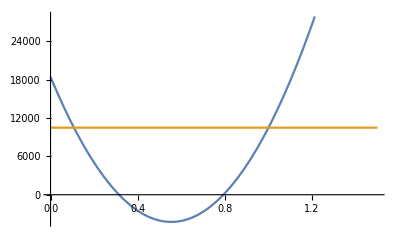

A_2^3 A_3 (B_1 c_2+c_2 ξ_1+c_1 (ξ_2-ξ_3))+c_2 ξ_1 (A_3+B_1+ξ_1+ξ_2+ξ_3) (A_3 (ξ_2^2+B_2 (ξ_2-ξ_3))-B_2 ξ_3^2)+A_2^2 A_3 (B_2 c_2 ξ_1+c_2 ξ_1^2+B_2 c_1 ξ_2+3 c_2 ξ_1 ξ_2+2 c_1 ξ_2^2+A_3 (B_1 c_2+c_2 ξ_1+c_1 (ξ_2-ξ_3))-B_2 c_1 ξ_3+c_2 ξ_1 ξ_3-c_1 ξ_3^2+B_1 c_2 (B_2+ξ_1+2 (ξ_2+ξ_3)))+A_1 c_2 (A_2^3 A_3+A_2^2 A_3 (A_3+B_2+ξ_1+2 ξ_2+2 ξ_3)+ξ_1 (A_3 (ξ_2^2+B_2 (ξ_2-ξ_3))-B_2 ξ_3^2)+A_2 A_3 (2 ξ_1 ξ_2+ξ_2^2+2 ξ_2 ξ_3+ξ_3^2+A_3 (B_2+ξ_2+ξ_3)+B_2 (ξ_1+ξ_2+ξ_3)))+A_2 (-B_2 c_2 ξ_1 ξ_3^2+A_3^2 (ξ_2 (2 c_2 ξ_1+c_1 ξ_2)+B_2 (c_2 ξ_1+c_1 (ξ_2-ξ_3))+B_1 c_2 (B_2+ξ_2+ξ_3))+A_3 (B_1 c_2 (2 ξ_1 ξ_2+(ξ_2+ξ_3)^2+B_2 (ξ_1+ξ_2+ξ_3))+ξ_2 (c_1 ξ_2 (ξ_2+ξ_3)+c_2 ξ_1 (2 ξ_1+3 ξ_2+2 ξ_3))+B_2 (c_2 ξ_1 (ξ_1+2 ξ_2)+c_1 (ξ_2^2-ξ_3^2))))

```mathematica
params={Subscript[A, 1]->3,Subscript[A, 2]->2,Subscript[A, 3]->2,Subscript[B, 1]->2,Subscript[B, 2]->4,Subscript[ξ, 1]->2,Subscript[ξ, 2]->4,Subscript[ξ, 3]->2,Subscript[c, 1]->2,Subscript[c, 2]->3}
remainingpoly/.params
Plot[{remainingpoly/.params,-Subscript[ξ, 3] (Subscript[A, 2]+Subscript[A, 3]+Subscript[ξ, 2]+Subscript[ξ, 3])opteq/.params},{λ ,0,1.5}]
```

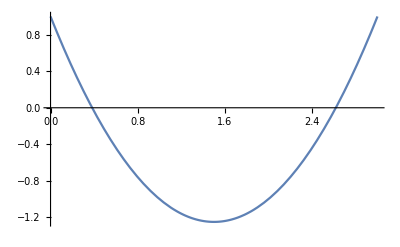

```mathematica
Plot[x^2 - 3 x + 1,{x,0,3}]
```

```mathematica
Factor[-Subscript[ξ, 3] (Subscript[A, 2]+Subscript[A, 3]+Subscript[ξ, 2]+Subscript[ξ, 3]) opteq /cof0]
```

(ξ_3 (A_2+A_3+ξ_2+ξ_3) (A_1 A_2 c_2 ξ_1+A_2 B_1 c_2 ξ_1+A_1 B_2 c_2 ξ_1+B_1 B_2 c_2 ξ_1+A_2 c_2 ξ_1^2+B_2 c_2 ξ_1^2-A_1 A_2 c_2 ξ_2-A_2 B_1 c_2 ξ_2-A_1 B_2 c_2 ξ_2-B_1 B_2 c_2 ξ_2+A_1 c_2 ξ_1 ξ_2+B_1 c_2 ξ_1 ξ_2+c_2 ξ_1^2 ξ_2-A_2 c_1 ξ_2^2-B_2 c_1 ξ_2^2-A_1 c_2 ξ_2^2-B_1 c_2 ξ_2^2-c_1 ξ_2^3+A_2 c_1 ξ_2 ξ_3+B_2 c_1 ξ_2 ξ_3-A_1 c_2 ξ_2 ξ_3-B_1 c_2 ξ_2 ξ_3))/(-A_1 A_2^3 A_3 c_2-A_1 A_2^2 A_3^2 c_2-A_2^3 A_3 B_1 c_2-A_2^2 A_3^2 B_1 c_2-A_1 A_2^2 A_3 B_2 c_2-A_1 A_2 A_3^2 B_2 c_2-A_2^2 A_3 B_1 B_2 c_2-A_2 A_3^2 B_1 B_2 c_2-A_1 A_2^2 A_3 c_2 ξ_1-A_2^3 A_3 c_2 ξ_1-A_2^2 A_3^2 c_2 ξ_1-A_2^2 A_3 B_1 c_2 ξ_1-A_1 A_2 A_3 B_2 c_2 ξ_1-A_2^2 A_3 B_2 c_2 ξ_1-A_2 A_3^2 B_2 c_2 ξ_1-A_2 A_3 B_1 B_2 c_2 ξ_1-A_2^2 A_3 c_2 ξ_1^2-A_2 A_3 B_2 c_2 ξ_1^2-A_2^3 A_3 c_1 ξ_2-A_2^2 A_3^2 c_1 ξ_2-A_2^2 A_3 B_2 c_1 ξ_2-A_2 A_3^2 B_2 c_1 ξ_2-2 A_1 A_2^2 A_3 c_2 ξ_2-A_1 A_2 A_3^2 c_2 ξ_2-2 A_2^2 A_3 B_1 c_2 ξ_2-A_2 A_3^2 B_1 c_2 ξ_2-A_1 A_2 A_3 B_2 c_2 ξ_2-A_2 A_3 B_1 B_2 c_2 ξ_2-2 A_1 A_2 A_3 c_2 ξ_1 ξ_2-3 A_2^2 A_3 c_2 ξ_1 ξ_2-2 A_2 A_3^2 c_2 ξ_1 ξ_2-2 A_2 A_3 B_1 c_2 ξ_1 ξ_2-A_1 A_3 B_2 c_2 ξ_1 ξ_2-2 A_2 A_3 B_2 c_2 ξ_1 ξ_2-A_3^2 B_2 c_2 ξ_1 ξ_2-A_3 B_1 B_2 c_2 ξ_1 ξ_2-2 A_2 A_3 c_2 ξ_1^2 ξ_2-A_3 B_2 c_2 ξ_1^2 ξ_2-2 A_2^2 A_3 c_1 ξ_2^2-A_2 A_3^2 c_1 ξ_2^2-A_2 A_3 B_2 c_1 ξ_2^2-A_1 A_2 A_3 c_2 ξ_2^2-A_2 A_3 B_1 c_2 ξ_2^2-A_1 A_3 c_2 ξ_1 ξ_2^2-3 A_2 A_3 c_2 ξ_1 ξ_2^2-A_3^2 c_2 ξ_1 ξ_2^2-A_3 B_1 c_2 ξ_1 ξ_2^2-A_3 B_2 c_2 ξ_1 ξ_2^2-A_3 c_2 ξ_1^2 ξ_2^2-A_2 A_3 c_1 ξ_2^3-A_3 c_2 ξ_1 ξ_2^3+A_2^3 A_3 c_1 ξ_3+A_2^2 A_3^2 c_1 ξ_3+A_2^2 A_3 B_2 c_1 ξ_3+A_2 A_3^2 B_2 c_1 ξ_3-2 A_1 A_2^2 A_3 c_2 ξ_3-A_1 A_2 A_3^2 c_2 ξ_3-2 A_2^2 A_3 B_1 c_2 ξ_3-A_2 A_3^2 B_1 c_2 ξ_3-A_1 A_2 A_3 B_2 c_2 ξ_3-A_2 A_3 B_1 B_2 c_2 ξ_3-A_2^2 A_3 c_2 ξ_1 ξ_3+A_1 A_3 B_2 c_2 ξ_1 ξ_3+A_3^2 B_2 c_2 ξ_1 ξ_3+A_3 B_1 B_2 c_2 ξ_1 ξ_3+A_3 B_2 c_2 ξ_1^2 ξ_3-2 A_1 A_2 A_3 c_2 ξ_2 ξ_3-2 A_2 A_3 B_1 c_2 ξ_2 ξ_3-2 A_2 A_3 c_2 ξ_1 ξ_2 ξ_3-A_2 A_3 c_1 ξ_2^2 ξ_3-A_3 c_2 ξ_1 ξ_2^2 ξ_3+A_2^2 A_3 c_1 ξ_3^2+A_2 A_3 B_2 c_1 ξ_3^2-A_1 A_2 A_3 c_2 ξ_3^2-A_2 A_3 B_1 c_2 ξ_3^2+A_1 B_2 c_2 ξ_1 ξ_3^2+A_2 B_2 c_2 ξ_1 ξ_3^2+2 A_3 B_2 c_2 ξ_1 ξ_3^2+B_1 B_2 c_2 ξ_1 ξ_3^2+B_2 c_2 ξ_1^2 ξ_3^2+B_2 c_2 ξ_1 ξ_2 ξ_3^2+B_2 c_2 ξ_1 ξ_3^3)

```mathematica
xxi={Subscript[x, 1]->Subscript[A, 1]+Subscript[ξ, 1],Subscript[x, 2]->Subscript[A, 2]+Subscript[ξ, 2],Subscript[x, 3]->Subscript[A, 3]+Subscript[ξ, 3]}
opteqlambda=opteqlambda/.xxi;
CoefficientList[opteqlambda,λ]//Factor
Collect[opteqlambda,λ,Factor]
opteqlambda/.{λ->1}/.xxi//Factor
```

{x_1→A_1+ξ_1,x_2→A_2+ξ_2,x_3→A_3+ξ_3}

{{c_2 (A_2+B_2+ξ_2) (A_1+A_2+A_3+ξ_1+ξ_2+ξ_3)^2,-c_2 (A_2+B_2+ξ_2) (A_1+A_2+A_3+ξ_1+ξ_2+ξ_3) (A_1+2 A_2+2 A_3-B_1+2 ξ_2+2 ξ_3),A_1 A_2^2 c_2+A_2^3 c_2+A_1 A_2 A_3 c_2+2 A_2^2 A_3 c_2+A_2 A_3^2 c_2-A_1 A_2 B_1 c_2-A_2^2 B_1 c_2-A_2 A_3 B_1 c_2+A_1 A_2 B_2 c_2+A_2^2 B_2 c_2+A_1 A_3 B_2 c_2+2 A_2 A_3 B_2 c_2+A_3^2 B_2 c_2-A_1 B_1 B_2 c_2-A_2 B_1 B_2 c_2-A_3 B_1 B_2 c_2+A_1 A_2 c_2 ξ_2+3 A_2^2 c_2 ξ_2+A_1 A_3 c_2 ξ_2+4 A_2 A_3 c_2 ξ_2+A_3^2 c_2 ξ_2-A_1 B_1 c_2 ξ_2-3 A_2 B_1 c_2 ξ_2-A_3 B_1 c_2 ξ_2+2 A_2 B_2 c_2 ξ_2+2 A_3 B_2 c_2 ξ_2-2 B_1 B_2 c_2 ξ_2-A_2 c_1 ξ_2^2-B_2 c_1 ξ_2^2+3 A_2 c_2 ξ_2^2+2 A_3 c_2 ξ_2^2-2 B_1 c_2 ξ_2^2+B_2 c_2 ξ_2^2-c_1 ξ_2^3+c_2 ξ_2^3+A_1 A_2 c_2 ξ_3+2 A_2^2 c_2 ξ_3+2 A_2 A_3 c_2 ξ_3-A_2 B_1 c_2 ξ_3+A_1 B_2 c_2 ξ_3+2 A_2 B_2 c_2 ξ_3+2 A_3 B_2 c_2 ξ_3-B_1 B_2 c_2 ξ_3+A_2 c_1 ξ_2 ξ_3+B_2 c_1 ξ_2 ξ_3+4 A_2 c_2 ξ_2 ξ_3+2 A_3 c_2 ξ_2 ξ_3-2 B_1 c_2 ξ_2 ξ_3+2 B_2 c_2 ξ_2 ξ_3+2 c_2 ξ_2^2 ξ_3+A_2 c_2 ξ_3^2+B_2 c_2 ξ_3^2+c_2 ξ_2 ξ_3^2}}

{c_2 (A_2+B_2+ξ_2) (A_1+A_2+A_3+ξ_1+ξ_2+ξ_3)^2-λ c_2 (A_2+B_2+ξ_2) (A_1+A_2+A_3+ξ_1+ξ_2+ξ_3) (A_1+2 A_2+2 A_3-B_1+2 ξ_2+2 ξ_3)+λ^2 (A_1 A_2^2 c_2+A_2^3 c_2+A_1 A_2 A_3 c_2+2 A_2^2 A_3 c_2+A_2 A_3^2 c_2-A_1 A_2 B_1 c_2-A_2^2 B_1 c_2-A_2 A_3 B_1 c_2+A_1 A_2 B_2 c_2+A_2^2 B_2 c_2+A_1 A_3 B_2 c_2+2 A_2 A_3 B_2 c_2+A_3^2 B_2 c_2-A_1 B_1 B_2 c_2-A_2 B_1 B_2 c_2-A_3 B_1 B_2 c_2+A_1 A_2 c_2 ξ_2+3 A_2^2 c_2 ξ_2+A_1 A_3 c_2 ξ_2+4 A_2 A_3 c_2 ξ_2+A_3^2 c_2 ξ_2-A_1 B_1 c_2 ξ_2-3 A_2 B_1 c_2 ξ_2-A_3 B_1 c_2 ξ_2+2 A_2 B_2 c_2 ξ_2+2 A_3 B_2 c_2 ξ_2-2 B_1 B_2 c_2 ξ_2-A_2 c_1 ξ_2^2-B_2 c_1 ξ_2^2+3 A_2 c_2 ξ_2^2+2 A_3 c_2 ξ_2^2-2 B_1 c_2 ξ_2^2+B_2 c_2 ξ_2^2-c_1 ξ_2^3+c_2 ξ_2^3+A_1 A_2 c_2 ξ_3+2 A_2^2 c_2 ξ_3+2 A_2 A_3 c_2 ξ_3-A_2 B_1 c_2 ξ_3+A_1 B_2 c_2 ξ_3+2 A_2 B_2 c_2 ξ_3+2 A_3 B_2 c_2 ξ_3-B_1 B_2 c_2 ξ_3+A_2 c_1 ξ_2 ξ_3+B_2 c_1 ξ_2 ξ_3+4 A_2 c_2 ξ_2 ξ_3+2 A_3 c_2 ξ_2 ξ_3-2 B_1 c_2 ξ_2 ξ_3+2 B_2 c_2 ξ_2 ξ_3+2 c_2 ξ_2^2 ξ_3+A_2 c_2 ξ_3^2+B_2 c_2 ξ_3^2+c_2 ξ_2 ξ_3^2)}

{A_1 A_2 c_2 ξ_1+A_2 B_1 c_2 ξ_1+A_1 B_2 c_2 ξ_1+B_1 B_2 c_2 ξ_1+A_2 c_2 ξ_1^2+B_2 c_2 ξ_1^2-A_1 A_2 c_2 ξ_2-A_2 B_1 c_2 ξ_2-A_1 B_2 c_2 ξ_2-B_1 B_2 c_2 ξ_2+A_1 c_2 ξ_1 ξ_2+B_1 c_2 ξ_1 ξ_2+c_2 ξ_1^2 ξ_2-A_2 c_1 ξ_2^2-B_2 c_1 ξ_2^2-A_1 c_2 ξ_2^2-B_1 c_2 ξ_2^2-c_1 ξ_2^3+A_2 c_1 ξ_2 ξ_3+B_2 c_1 ξ_2 ξ_3-A_1 c_2 ξ_2 ξ_3-B_1 c_2 ξ_2 ξ_3}

```mathematica
c2sol=Solve[PQfac/(λ-1)==0,Subscript[c, 2]][[1]]
```

{c_2→(-A_2^3 A_3 c_1 ξ_2+2 λ A_2^3 A_3 c_1 ξ_2-λ^2 A_2^3 A_3 c_1 ξ_2-A_2^2 A_3^2 c_1 ξ_2+2 λ A_2^2 A_3^2 c_1 ξ_2-λ^2 A_2^2 A_3^2 c_1 ξ_2-A_2^2 A_3 B_2 c_1 ξ_2+2 λ A_2^2 A_3 B_2 c_1 ξ_2-λ^2 A_2^2 A_3 B_2 c_1 ξ_2-A_2 A_3^2 B_2 c_1 ξ_2+2 λ A_2 A_3^2 B_2 c_1 ξ_2-λ^2 A_2 A_3^2 B_2 c_1 ξ_2-2 A_2^2 A_3 c_1 ξ_2^2+5 λ A_2^2 A_3 c_1 ξ_2^2-3 λ^2 A_2^2 A_3 c_1 ξ_2^2-A_2 A_3^2 c_1 ξ_2^2+3 λ A_2 A_3^2 c_1 ξ_2^2-2 λ^2 A_2 A_3^2 c_1 ξ_2^2-A_2 A_3 B_2 c_1 ξ_2^2+3 λ A_2 A_3 B_2 c_1 ξ_2^2-2 λ^2 A_2 A_3 B_2 c_1 ξ_2^2+λ A_3^2 B_2 c_1 ξ_2^2-λ^2 A_3^2 B_2 c_1 ξ_2^2-A_2 A_3 c_1 ξ_2^3+4 λ A_2 A_3 c_1 ξ_2^3-3 λ^2 A_2 A_3 c_1 ξ_2^3+λ A_3^2 c_1 ξ_2^3-λ^2 A_3^2 c_1 ξ_2^3+λ A_3 B_2 c_1 ξ_2^3-λ^2 A_3 B_2 c_1 ξ_2^3+λ A_3 c_1 ξ_2^4-λ^2 A_3 c_1 ξ_2^4+A_2^3 A_3 c_1 ξ_3-2 λ A_2^3 A_3 c_1 ξ_3+λ^2 A_2^3 A_3 c_1 ξ_3+A_2^2 A_3^2 c_1 ξ_3-2 λ A_2^2 A_3^2 c_1 ξ_3+λ^2 A_2^2 A_3^2 c_1 ξ_3+A_2^2 A_3 B_2 c_1 ξ_3-2 λ A_2^2 A_3 B_2 c_1 ξ_3+λ^2 A_2^2 A_3 B_2 c_1 ξ_3+A_2 A_3^2 B_2 c_1 ξ_3-2 λ A_2 A_3^2 B_2 c_1 ξ_3+λ^2 A_2 A_3^2 B_2 c_1 ξ_3+λ A_2^3 c_1 ξ_2 ξ_3-λ^2 A_2^3 c_1 ξ_2 ξ_3-λ A_2 A_3^2 c_1 ξ_2 ξ_3+λ^2 A_2 A_3^2 c_1 ξ_2 ξ_3+λ A_2^2 B_2 c_1 ξ_2 ξ_3-λ^2 A_2^2 B_2 c_1 ξ_2 ξ_3-λ A_3^2 B_2 c_1 ξ_2 ξ_3+λ^2 A_3^2 B_2 c_1 ξ_2 ξ_3+2 λ A_2^2 c_1 ξ_2^2 ξ_3-3 λ^2 A_2^2 c_1 ξ_2^2 ξ_3-A_2 A_3 c_1 ξ_2^2 ξ_3+3 λ A_2 A_3 c_1 ξ_2^2 ξ_3-3 λ^2 A_2 A_3 c_1 ξ_2^2 ξ_3+λ A_2 B_2 c_1 ξ_2^2 ξ_3-2 λ^2 A_2 B_2 c_1 ξ_2^2 ξ_3-λ^2 A_3 B_2 c_1 ξ_2^2 ξ_3+λ A_2 c_1 ξ_2^3 ξ_3-3 λ^2 A_2 c_1 ξ_2^3 ξ_3+λ A_3 c_1 ξ_2^3 ξ_3-2 λ^2 A_3 c_1 ξ_2^3 ξ_3-λ^2 B_2 c_1 ξ_2^3 ξ_3-λ^2 c_1 ξ_2^4 ξ_3-λ A_2^3 c_1 ξ_3^2+λ^2 A_2^3 c_1 ξ_3^2+A_2^2 A_3 c_1 ξ_3^2-3 λ A_2^2 A_3 c_1 ξ_3^2+2 λ^2 A_2^2 A_3 c_1 ξ_3^2-λ A_2^2 B_2 c_1 ξ_3^2+λ^2 A_2^2 B_2 c_1 ξ_3^2+A_2 A_3 B_2 c_1 ξ_3^2-3 λ A_2 A_3 B_2 c_1 ξ_3^2+2 λ^2 A_2 A_3 B_2 c_1 ξ_3^2+λ^2 A_2^2 c_1 ξ_2 ξ_3^2-λ A_2 A_3 c_1 ξ_2 ξ_3^2+2 λ^2 A_2 A_3 c_1 ξ_2 ξ_3^2+λ^2 A_2 B_2 c_1 ξ_2 ξ_3^2-λ A_3 B_2 c_1 ξ_2 ξ_3^2+2 λ^2 A_3 B_2 c_1 ξ_2 ξ_3^2+λ A_2 c_1 ξ_2^2 ξ_3^2-λ^2 A_2 c_1 ξ_2^2 ξ_3^2-λ^2 c_1 ξ_2^3 ξ_3^2-λ A_2^2 c_1 ξ_3^3+λ^2 A_2^2 c_1 ξ_3^3-λ A_2 B_2 c_1 ξ_3^3+λ^2 A_2 B_2 c_1 ξ_3^3+λ^2 A_2 c_1 ξ_2 ξ_3^3+λ^2 B_2 c_1 ξ_2 ξ_3^3)/(A_1 A_2^3 A_3-2 λ A_1 A_2^3 A_3+λ^2 A_1 A_2^3 A_3+A_1 A_2^2 A_3^2-2 λ A_1 A_2^2 A_3^2+λ^2 A_1 A_2^2 A_3^2+A_2^3 A_3 B_1-2 λ A_2^3 A_3 B_1+λ^2 A_2^3 A_3 B_1+A_2^2 A_3^2 B_1-2 λ A_2^2 A_3^2 B_1+λ^2 A_2^2 A_3^2 B_1+A_1 A_2^2 A_3 B_2-2 λ A_1 A_2^2 A_3 B_2+λ^2 A_1 A_2^2 A_3 B_2+A_1 A_2 A_3^2 B_2-2 λ A_1 A_2 A_3^2 B_2+λ^2 A_1 A_2 A_3^2 B_2+A_2^2 A_3 B_1 B_2-2 λ A_2^2 A_3 B_1 B_2+λ^2 A_2^2 A_3 B_1 B_2+A_2 A_3^2 B_1 B_2-2 λ A_2 A_3^2 B_1 B_2+λ^2 A_2 A_3^2 B_1 B_2+A_1 A_2^2 A_3 ξ_1-λ A_1 A_2^2 A_3 ξ_1+A_2^3 A_3 ξ_1-2 λ A_2^3 A_3 ξ_1+λ^2 A_2^3 A_3 ξ_1+A_2^2 A_3^2 ξ_1-2 λ A_2^2 A_3^2 ξ_1+λ^2 A_2^2 A_3^2 ξ_1+A_2^2 A_3 B_1 ξ_1-λ A_2^2 A_3 B_1 ξ_1+A_1 A_2 A_3 B_2 ξ_1-λ A_1 A_2 A_3 B_2 ξ_1+A_2^2 A_3 B_2 ξ_1-2 λ A_2^2 A_3 B_2 ξ_1+λ^2 A_2^2 A_3 B_2 ξ_1+A_2 A_3^2 B_2 ξ_1-2 λ A_2 A_3^2 B_2 ξ_1+λ^2 A_2 A_3^2 B_2 ξ_1+A_2 A_3 B_1 B_2 ξ_1-λ A_2 A_3 B_1 B_2 ξ_1+A_2^2 A_3 ξ_1^2-λ A_2^2 A_3 ξ_1^2+A_2 A_3 B_2 ξ_1^2-λ A_2 A_3 B_2 ξ_1^2+2 A_1 A_2^2 A_3 ξ_2-5 λ A_1 A_2^2 A_3 ξ_2+3 λ^2 A_1 A_2^2 A_3 ξ_2+A_1 A_2 A_3^2 ξ_2-3 λ A_1 A_2 A_3^2 ξ_2+2 λ^2 A_1 A_2 A_3^2 ξ_2+2 A_2^2 A_3 B_1 ξ_2-5 λ A_2^2 A_3 B_1 ξ_2+3 λ^2 A_2^2 A_3 B_1 ξ_2+A_2 A_3^2 B_1 ξ_2-3 λ A_2 A_3^2 B_1 ξ_2+2 λ^2 A_2 A_3^2 B_1 ξ_2+A_1 A_2 A_3 B_2 ξ_2-3 λ A_1 A_2 A_3 B_2 ξ_2+2 λ^2 A_1 A_2 A_3 B_2 ξ_2-λ A_1 A_3^2 B_2 ξ_2+λ^2 A_1 A_3^2 B_2 ξ_2+A_2 A_3 B_1 B_2 ξ_2-3 λ A_2 A_3 B_1 B_2 ξ_2+2 λ^2 A_2 A_3 B_1 B_2 ξ_2-λ A_3^2 B_1 B_2 ξ_2+λ^2 A_3^2 B_1 B_2 ξ_2+2 A_1 A_2 A_3 ξ_1 ξ_2-2 λ A_1 A_2 A_3 ξ_1 ξ_2+3 A_2^2 A_3 ξ_1 ξ_2-6 λ A_2^2 A_3 ξ_1 ξ_2+3 λ^2 A_2^2 A_3 ξ_1 ξ_2+2 A_2 A_3^2 ξ_1 ξ_2-4 λ A_2 A_3^2 ξ_1 ξ_2+2 λ^2 A_2 A_3^2 ξ_1 ξ_2+2 A_2 A_3 B_1 ξ_1 ξ_2-2 λ A_2 A_3 B_1 ξ_1 ξ_2+A_1 A_3 B_2 ξ_1 ξ_2-λ A_1 A_3 B_2 ξ_1 ξ_2+2 A_2 A_3 B_2 ξ_1 ξ_2-4 λ A_2 A_3 B_2 ξ_1 ξ_2+2 λ^2 A_2 A_3 B_2 ξ_1 ξ_2+A_3^2 B_2 ξ_1 ξ_2-2 λ A_3^2 B_2 ξ_1 ξ_2+λ^2 A_3^2 B_2 ξ_1 ξ_2+A_3 B_1 B_2 ξ_1 ξ_2-λ A_3 B_1 B_2 ξ_1 ξ_2+2 A_2 A_3 ξ_1^2 ξ_2-2 λ A_2 A_3 ξ_1^2 ξ_2+A_3 B_2 ξ_1^2 ξ_2-λ A_3 B_2 ξ_1^2 ξ_2+A_1 A_2 A_3 ξ_2^2-4 λ A_1 A_2 A_3 ξ_2^2+3 λ^2 A_1 A_2 A_3 ξ_2^2-λ A_1 A_3^2 ξ_2^2+λ^2 A_1 A_3^2 ξ_2^2+A_2 A_3 B_1 ξ_2^2-4 λ A_2 A_3 B_1 ξ_2^2+3 λ^2 A_2 A_3 B_1 ξ_2^2-λ A_3^2 B_1 ξ_2^2+λ^2 A_3^2 B_1 ξ_2^2-λ A_1 A_3 B_2 ξ_2^2+λ^2 A_1 A_3 B_2 ξ_2^2-λ A_3 B_1 B_2 ξ_2^2+λ^2 A_3 B_1 B_2 ξ_2^2+A_1 A_3 ξ_1 ξ_2^2-λ A_1 A_3 ξ_1 ξ_2^2+3 A_2 A_3 ξ_1 ξ_2^2-6 λ A_2 A_3 ξ_1 ξ_2^2+3 λ^2 A_2 A_3 ξ_1 ξ_2^2+A_3^2 ξ_1 ξ_2^2-2 λ A_3^2 ξ_1 ξ_2^2+λ^2 A_3^2 ξ_1 ξ_2^2+A_3 B_1 ξ_1 ξ_2^2-λ A_3 B_1 ξ_1 ξ_2^2+A_3 B_2 ξ_1 ξ_2^2-2 λ A_3 B_2 ξ_1 ξ_2^2+λ^2 A_3 B_2 ξ_1 ξ_2^2+A_3 ξ_1^2 ξ_2^2-λ A_3 ξ_1^2 ξ_2^2-λ A_1 A_3 ξ_2^3+λ^2 A_1 A_3 ξ_2^3-λ A_3 B_1 ξ_2^3+λ^2 A_3 B_1 ξ_2^3+A_3 ξ_1 ξ_2^3-2 λ A_3 ξ_1 ξ_2^3+λ^2 A_3 ξ_1 ξ_2^3-λ A_1 A_2^3 ξ_3+λ^2 A_1 A_2^3 ξ_3+2 A_1 A_2^2 A_3 ξ_3-5 λ A_1 A_2^2 A_3 ξ_3+3 λ^2 A_1 A_2^2 A_3 ξ_3+A_1 A_2 A_3^2 ξ_3-2 λ A_1 A_2 A_3^2 ξ_3+λ^2 A_1 A_2 A_3^2 ξ_3-λ A_2^3 B_1 ξ_3+λ^2 A_2^3 B_1 ξ_3+2 A_2^2 A_3 B_1 ξ_3-5 λ A_2^2 A_3 B_1 ξ_3+3 λ^2 A_2^2 A_3 B_1 ξ_3+A_2 A_3^2 B_1 ξ_3-2 λ A_2 A_3^2 B_1 ξ_3+λ^2 A_2 A_3^2 B_1 ξ_3-λ A_1 A_2^2 B_2 ξ_3+λ^2 A_1 A_2^2 B_2 ξ_3+A_1 A_2 A_3 B_2 ξ_3-3 λ A_1 A_2 A_3 B_2 ξ_3+2 λ^2 A_1 A_2 A_3 B_2 ξ_3-λ A_2^2 B_1 B_2 ξ_3+λ^2 A_2^2 B_1 B_2 ξ_3+A_2 A_3 B_1 B_2 ξ_3-3 λ A_2 A_3 B_1 B_2 ξ_3+2 λ^2 A_2 A_3 B_1 B_2 ξ_3-λ A_1 A_2^2 ξ_1 ξ_3-λ A_2^3 ξ_1 ξ_3+λ^2 A_2^3 ξ_1 ξ_3-λ A_1 A_2 A_3 ξ_1 ξ_3+A_2^2 A_3 ξ_1 ξ_3-4 λ A_2^2 A_3 ξ_1 ξ_3+3 λ^2 A_2^2 A_3 ξ_1 ξ_3-λ A_2 A_3^2 ξ_1 ξ_3+λ^2 A_2 A_3^2 ξ_1 ξ_3-λ A_2^2 B_1 ξ_1 ξ_3-λ A_2 A_3 B_1 ξ_1 ξ_3-λ A_1 A_2 B_2 ξ_1 ξ_3-λ A_2^2 B_2 ξ_1 ξ_3+λ^2 A_2^2 B_2 ξ_1 ξ_3-A_1 A_3 B_2 ξ_1 ξ_3-2 λ A_2 A_3 B_2 ξ_1 ξ_3+2 λ^2 A_2 A_3 B_2 ξ_1 ξ_3-A_3^2 B_2 ξ_1 ξ_3+λ A_3^2 B_2 ξ_1 ξ_3-λ A_2 B_1 B_2 ξ_1 ξ_3-A_3 B_1 B_2 ξ_1 ξ_3-λ A_2^2 ξ_1^2 ξ_3-λ A_2 A_3 ξ_1^2 ξ_3-λ A_2 B_2 ξ_1^2 ξ_3-A_3 B_2 ξ_1^2 ξ_3-2 λ A_1 A_2^2 ξ_2 ξ_3+3 λ^2 A_1 A_2^2 ξ_2 ξ_3+2 A_1 A_2 A_3 ξ_2 ξ_3-7 λ A_1 A_2 A_3 ξ_2 ξ_3+6 λ^2 A_1 A_2 A_3 ξ_2 ξ_3-λ A_1 A_3^2 ξ_2 ξ_3+λ^2 A_1 A_3^2 ξ_2 ξ_3-2 λ A_2^2 B_1 ξ_2 ξ_3+3 λ^2 A_2^2 B_1 ξ_2 ξ_3+2 A_2 A_3 B_1 ξ_2 ξ_3-7 λ A_2 A_3 B_1 ξ_2 ξ_3+6 λ^2 A_2 A_3 B_1 ξ_2 ξ_3-λ A_3^2 B_1 ξ_2 ξ_3+λ^2 A_3^2 B_1 ξ_2 ξ_3-λ A_1 A_2 B_2 ξ_2 ξ_3+2 λ^2 A_1 A_2 B_2 ξ_2 ξ_3-λ A_1 A_3 B_2 ξ_2 ξ_3+2 λ^2 A_1 A_3 B_2 ξ_2 ξ_3-λ A_2 B_1 B_2 ξ_2 ξ_3+2 λ^2 A_2 B_1 B_2 ξ_2 ξ_3-λ A_3 B_1 B_2 ξ_2 ξ_3+2 λ^2 A_3 B_1 B_2 ξ_2 ξ_3-2 λ A_1 A_2 ξ_1 ξ_2 ξ_3-3 λ A_2^2 ξ_1 ξ_2 ξ_3+3 λ^2 A_2^2 ξ_1 ξ_2 ξ_3-λ A_1 A_3 ξ_1 ξ_2 ξ_3+2 A_2 A_3 ξ_1 ξ_2 ξ_3-8 λ A_2 A_3 ξ_1 ξ_2 ξ_3+6 λ^2 A_2 A_3 ξ_1 ξ_2 ξ_3-λ A_3^2 ξ_1 ξ_2 ξ_3+λ^2 A_3^2 ξ_1 ξ_2 ξ_3-2 λ A_2 B_1 ξ_1 ξ_2 ξ_3-λ A_3 B_1 ξ_1 ξ_2 ξ_3-λ A_1 B_2 ξ_1 ξ_2 ξ_3-2 λ A_2 B_2 ξ_1 ξ_2 ξ_3+2 λ^2 A_2 B_2 ξ_1 ξ_2 ξ_3-2 λ A_3 B_2 ξ_1 ξ_2 ξ_3+2 λ^2 A_3 B_2 ξ_1 ξ_2 ξ_3-λ B_1 B_2 ξ_1 ξ_2 ξ_3-2 λ A_2 ξ_1^2 ξ_2 ξ_3-λ A_3 ξ_1^2 ξ_2 ξ_3-λ B_2 ξ_1^2 ξ_2 ξ_3-λ A_1 A_2 ξ_2^2 ξ_3+3 λ^2 A_1 A_2 ξ_2^2 ξ_3-2 λ A_1 A_3 ξ_2^2 ξ_3+3 λ^2 A_1 A_3 ξ_2^2 ξ_3-λ A_2 B_1 ξ_2^2 ξ_3+3 λ^2 A_2 B_1 ξ_2^2 ξ_3-2 λ A_3 B_1 ξ_2^2 ξ_3+3 λ^2 A_3 B_1 ξ_2^2 ξ_3+λ^2 A_1 B_2 ξ_2^2 ξ_3+λ^2 B_1 B_2 ξ_2^2 ξ_3-λ A_1 ξ_1 ξ_2^2 ξ_3-3 λ A_2 ξ_1 ξ_2^2 ξ_3+3 λ^2 A_2 ξ_1 ξ_2^2 ξ_3+A_3 ξ_1 ξ_2^2 ξ_3-4 λ A_3 ξ_1 ξ_2^2 ξ_3+3 λ^2 A_3 ξ_1 ξ_2^2 ξ_3-λ B_1 ξ_1 ξ_2^2 ξ_3-λ B_2 ξ_1 ξ_2^2 ξ_3+λ^2 B_2 ξ_1 ξ_2^2 ξ_3-λ ξ_1^2 ξ_2^2 ξ_3+λ^2 A_1 ξ_2^3 ξ_3+λ^2 B_1 ξ_2^3 ξ_3-λ ξ_1 ξ_2^3 ξ_3+λ^2 ξ_1 ξ_2^3 ξ_3-2 λ A_1 A_2^2 ξ_3^2+2 λ^2 A_1 A_2^2 ξ_3^2+A_1 A_2 A_3 ξ_3^2-3 λ A_1 A_2 A_3 ξ_3^2+2 λ^2 A_1 A_2 A_3 ξ_3^2-2 λ A_2^2 B_1 ξ_3^2+2 λ^2 A_2^2 B_1 ξ_3^2+A_2 A_3 B_1 ξ_3^2-3 λ A_2 A_3 B_1 ξ_3^2+2 λ^2 A_2 A_3 B_1 ξ_3^2-λ A_1 A_2 B_2 ξ_3^2+λ^2 A_1 A_2 B_2 ξ_3^2-λ A_2 B_1 B_2 ξ_3^2+λ^2 A_2 B_1 B_2 ξ_3^2-λ A_1 A_2 ξ_1 ξ_3^2-2 λ A_2^2 ξ_1 ξ_3^2+2 λ^2 A_2^2 ξ_1 ξ_3^2-2 λ A_2 A_3 ξ_1 ξ_3^2+2 λ^2 A_2 A_3 ξ_1 ξ_3^2-λ A_2 B_1 ξ_1 ξ_3^2-A_1 B_2 ξ_1 ξ_3^2-A_2 B_2 ξ_1 ξ_3^2+λ^2 A_2 B_2 ξ_1 ξ_3^2-2 A_3 B_2 ξ_1 ξ_3^2+2 λ A_3 B_2 ξ_1 ξ_3^2-B_1 B_2 ξ_1 ξ_3^2-λ A_2 ξ_1^2 ξ_3^2-B_2 ξ_1^2 ξ_3^2-2 λ A_1 A_2 ξ_2 ξ_3^2+4 λ^2 A_1 A_2 ξ_2 ξ_3^2-λ A_1 A_3 ξ_2 ξ_3^2+2 λ^2 A_1 A_3 ξ_2 ξ_3^2-2 λ A_2 B_1 ξ_2 ξ_3^2+4 λ^2 A_2 B_1 ξ_2 ξ_3^2-λ A_3 B_1 ξ_2 ξ_3^2+2 λ^2 A_3 B_1 ξ_2 ξ_3^2+λ^2 A_1 B_2 ξ_2 ξ_3^2+λ^2 B_1 B_2 ξ_2 ξ_3^2-λ A_1 ξ_1 ξ_2 ξ_3^2-4 λ A_2 ξ_1 ξ_2 ξ_3^2+4 λ^2 A_2 ξ_1 ξ_2 ξ_3^2-2 λ A_3 ξ_1 ξ_2 ξ_3^2+2 λ^2 A_3 ξ_1 ξ_2 ξ_3^2-λ B_1 ξ_1 ξ_2 ξ_3^2-B_2 ξ_1 ξ_2 ξ_3^2+λ^2 B_2 ξ_1 ξ_2 ξ_3^2-λ ξ_1^2 ξ_2 ξ_3^2+2 λ^2 A_1 ξ_2^2 ξ_3^2+2 λ^2 B_1 ξ_2^2 ξ_3^2-2 λ ξ_1 ξ_2^2 ξ_3^2+2 λ^2 ξ_1 ξ_2^2 ξ_3^2-λ A_1 A_2 ξ_3^3+λ^2 A_1 A_2 ξ_3^3-λ A_2 B_1 ξ_3^3+λ^2 A_2 B_1 ξ_3^3-λ A_2 ξ_1 ξ_3^3+λ^2 A_2 ξ_1 ξ_3^3-B_2 ξ_1 ξ_3^3+λ B_2 ξ_1 ξ_3^3+λ^2 A_1 ξ_2 ξ_3^3+λ^2 B_1 ξ_2 ξ_3^3-λ ξ_1 ξ_2 ξ_3^3+λ^2 ξ_1 ξ_2 ξ_3^3)}

```mathematica
Numerator[Factor[opteqlambda/.c2sol]]
```

{-(-1+λ) c_1 (A_2 ξ_2+B_2 ξ_2+ξ_2^2-A_2 ξ_3-B_2 ξ_3) (-A_1^2 A_2^3 A_3+2 λ A_1^2 A_2^3 A_3-λ^2 A_1^2 A_2^3 A_3-2 A_1 A_2^4 A_3+5 λ A_1 A_2^4 A_3-4 λ^2 A_1 A_2^4 A_3+λ^3 A_1 A_2^4 A_3-A_2^5 A_3+3 λ A_2^5 A_3-3 λ^2 A_2^5 A_3+λ^3 A_2^5 A_3-A_1^2 A_2^2 A_3^2+2 λ A_1^2 A_2^2 A_3^2-λ^2 A_1^2 A_2^2 A_3^2-4 A_1 A_2^3 A_3^2+10 λ A_1 A_2^3 A_3^2-8 λ^2 A_1 A_2^3 A_3^2+2 λ^3 A_1 A_2^3 A_3^2-3 A_2^4 A_3^2+9 λ A_2^4 A_3^2-9 λ^2 A_2^4 A_3^2+3 λ^3 A_2^4 A_3^2-2 A_1 A_2^2 A_3^3+5 λ A_1 A_2^2 A_3^3-4 λ^2 A_1 A_2^2 A_3^3+λ^3 A_1 A_2^2 A_3^3-3 A_2^3 A_3^3+9 λ A_2^3 A_3^3-9 λ^2 A_2^3 A_3^3+3 λ^3 A_2^3 A_3^3-A_2^2 A_3^4+3 λ A_2^2 A_3^4-3 λ^2 A_2^2 A_3^4+λ^3 A_2^2 A_3^4-λ A_1 A_2^3 A_3 B_1+2 λ^2 A_1 A_2^3 A_3 B_1-λ^3 A_1 A_2^3 A_3 B_1-λ A_2^4 A_3 B_1+2 λ^2 A_2^4 A_3 B_1-λ^3 A_2^4 A_3 B_1-λ A_1 A_2^2 A_3^2 B_1+2 λ^2 A_1 A_2^2 A_3^2 B_1-λ^3 A_1 A_2^2 A_3^2 B_1-2 λ A_2^3 A_3^2 B_1+4 λ^2 A_2^3 A_3^2 B_1-2 λ^3 A_2^3 A_3^2 B_1-λ A_2^2 A_3^3 B_1+2 λ^2 A_2^2 A_3^3 B_1-λ^3 A_2^2 A_3^3 B_1-A_1^2 A_2^2 A_3 B_2+2 λ A_1^2 A_2^2 A_3 B_2-λ^2 A_1^2 A_2^2 A_3 B_2-2 A_1 A_2^3 A_3 B_2+5 λ A_1 A_2^3 A_3 B_2-4 λ^2 A_1 A_2^3 A_3 B_2+λ^3 A_1 A_2^3 A_3 B_2-A_2^4 A_3 B_2+3 λ A_2^4 A_3 B_2-3 λ^2 A_2^4 A_3 B_2+λ^3 A_2^4 A_3 B_2-A_1^2 A_2 A_3^2 B_2+2 λ A_1^2 A_2 A_3^2 B_2-λ^2 A_1^2 A_2 A_3^2 B_2-4 A_1 A_2^2 A_3^2 B_2+10 λ A_1 A_2^2 A_3^2 B_2-8 λ^2 A_1 A_2^2 A_3^2 B_2+2 λ^3 A_1 A_2^2 A_3^2 B_2-3 A_2^3 A_3^2 B_2+9 λ A_2^3 A_3^2 B_2-9 λ^2 A_2^3 A_3^2 B_2+3 λ^3 A_2^3 A_3^2 B_2-2 A_1 A_2 A_3^3 B_2+5 λ A_1 A_2 A_3^3 B_2-4 λ^2 A_1 A_2 A_3^3 B_2+λ^3 A_1 A_2 A_3^3 B_2-3 A_2^2 A_3^3 B_2+9 λ A_2^2 A_3^3 B_2-9 λ^2 A_2^2 A_3^3 B_2+3 λ^3 A_2^2 A_3^3 B_2-A_2 A_3^4 B_2+3 λ A_2 A_3^4 B_2-3 λ^2 A_2 A_3^4 B_2+λ^3 A_2 A_3^4 B_2-λ A_1 A_2^2 A_3 B_1 B_2+2 λ^2 A_1 A_2^2 A_3 B_1 B_2-λ^3 A_1 A_2^2 A_3 B_1 B_2-λ A_2^3 A_3 B_1 B_2+2 λ^2 A_2^3 A_3 B_1 B_2-λ^3 A_2^3 A_3 B_1 B_2-λ A_1 A_2 A_3^2 B_1 B_2+2 λ^2 A_1 A_2 A_3^2 B_1 B_2-λ^3 A_1 A_2 A_3^2 B_1 B_2-2 λ A_2^2 A_3^2 B_1 B_2+4 λ^2 A_2^2 A_3^2 B_1 B_2-2 λ^3 A_2^2 A_3^2 B_1 B_2-λ A_2 A_3^3 B_1 B_2+1412+2 λ^3 A_1 ξ_2^3 ξ_3^2+3 λ A_2 ξ_2^3 ξ_3^2-15 λ^2 A_2 ξ_2^3 ξ_3^2+12 λ^3 A_2 ξ_2^3 ξ_3^2+3 λ A_3 ξ_2^3 ξ_3^2-12 λ^2 A_3 ξ_2^3 ξ_3^2+9 λ^3 A_3 ξ_2^3 ξ_3^2-2 λ^3 B_1 ξ_2^3 ξ_3^2-3 λ^2 B_2 ξ_2^3 ξ_3^2+3 λ^3 B_2 ξ_2^3 ξ_3^2-4 λ^2 ξ_1 ξ_2^3 ξ_3^2+2 λ^3 ξ_1 ξ_2^3 ξ_3^2-3 λ^2 ξ_2^4 ξ_3^2+3 λ^3 ξ_2^4 ξ_3^2+2 λ A_1 A_2^2 ξ_3^3-3 λ^2 A_1 A_2^2 ξ_3^3+λ^3 A_1 A_2^2 ξ_3^3+3 λ A_2^3 ξ_3^3-6 λ^2 A_2^3 ξ_3^3+3 λ^3 A_2^3 ξ_3^3-A_2^2 A_3 ξ_3^3+6 λ A_2^2 A_3 ξ_3^3-9 λ^2 A_2^2 A_3 ξ_3^3+4 λ^3 A_2^2 A_3 ξ_3^3+λ^2 A_2^2 B_1 ξ_3^3-λ^3 A_2^2 B_1 ξ_3^3+2 λ A_1 A_2 B_2 ξ_3^3-3 λ^2 A_1 A_2 B_2 ξ_3^3+λ^3 A_1 A_2 B_2 ξ_3^3+3 λ A_2^2 B_2 ξ_3^3-6 λ^2 A_2^2 B_2 ξ_3^3+3 λ^3 A_2^2 B_2 ξ_3^3-A_2 A_3 B_2 ξ_3^3+6 λ A_2 A_3 B_2 ξ_3^3-9 λ^2 A_2 A_3 B_2 ξ_3^3+4 λ^3 A_2 A_3 B_2 ξ_3^3+λ^2 A_2 B_1 B_2 ξ_3^3-λ^3 A_2 B_1 B_2 ξ_3^3+2 λ A_2^2 ξ_1 ξ_3^3-2 λ^2 A_2^2 ξ_1 ξ_3^3+2 λ A_2 B_2 ξ_1 ξ_3^3-2 λ^2 A_2 B_2 ξ_1 ξ_3^3+2 λ A_1 A_2 ξ_2 ξ_3^3-5 λ^2 A_1 A_2 ξ_2 ξ_3^3+2 λ^3 A_1 A_2 ξ_2 ξ_3^3+6 λ A_2^2 ξ_2 ξ_3^3-15 λ^2 A_2^2 ξ_2 ξ_3^3+9 λ^3 A_2^2 ξ_2 ξ_3^3-A_2 A_3 ξ_2 ξ_3^3+7 λ A_2 A_3 ξ_2 ξ_3^3-14 λ^2 A_2 A_3 ξ_2 ξ_3^3+8 λ^3 A_2 A_3 ξ_2 ξ_3^3+λ^2 A_2 B_1 ξ_2 ξ_3^3-2 λ^3 A_2 B_1 ξ_2 ξ_3^3-2 λ^2 A_1 B_2 ξ_2 ξ_3^3+λ^3 A_1 B_2 ξ_2 ξ_3^3+3 λ A_2 B_2 ξ_2 ξ_3^3-9 λ^2 A_2 B_2 ξ_2 ξ_3^3+6 λ^3 A_2 B_2 ξ_2 ξ_3^3+λ A_3 B_2 ξ_2 ξ_3^3-5 λ^2 A_3 B_2 ξ_2 ξ_3^3+4 λ^3 A_3 B_2 ξ_2 ξ_3^3-λ^3 B_1 B_2 ξ_2 ξ_3^3+2 λ A_2 ξ_1 ξ_2 ξ_3^3-4 λ^2 A_2 ξ_1 ξ_2 ξ_3^3+λ^3 A_2 ξ_1 ξ_2 ξ_3^3-λ^2 B_2 ξ_1 ξ_2 ξ_3^3-2 λ^2 A_1 ξ_2^2 ξ_3^3+λ^3 A_1 ξ_2^2 ξ_3^3+3 λ A_2 ξ_2^2 ξ_3^3-12 λ^2 A_2 ξ_2^2 ξ_3^3+9 λ^3 A_2 ξ_2^2 ξ_3^3+λ A_3 ξ_2^2 ξ_3^3-5 λ^2 A_3 ξ_2^2 ξ_3^3+4 λ^3 A_3 ξ_2^2 ξ_3^3-λ^3 B_1 ξ_2^2 ξ_3^3-3 λ^2 B_2 ξ_2^2 ξ_3^3+3 λ^3 B_2 ξ_2^2 ξ_3^3-2 λ^2 ξ_1 ξ_2^2 ξ_3^3+λ^3 ξ_1 ξ_2^2 ξ_3^3-3 λ^2 ξ_2^3 ξ_3^3+3 λ^3 ξ_2^3 ξ_3^3+λ A_2^2 ξ_3^4-2 λ^2 A_2^2 ξ_3^4+λ^3 A_2^2 ξ_3^4+λ A_2 B_2 ξ_3^4-2 λ^2 A_2 B_2 ξ_3^4+λ^3 A_2 B_2 ξ_3^4+λ A_2 ξ_2 ξ_3^4-3 λ^2 A_2 ξ_2 ξ_3^4+2 λ^3 A_2 ξ_2 ξ_3^4-λ^2 B_2 ξ_2 ξ_3^4+λ^3 B_2 ξ_2 ξ_3^4-λ^2 ξ_2^2 ξ_3^4+λ^3 ξ_2^2 ξ_3^4)}
 |  |  |  |